## Introduction

This notebook is a collection of numbers of group-like algebras, algebras with a single binary operation on a set.

### In General

The data are in form numdata[arg] where arg is a text string that contains various abbreviations separated by spaces. Here are some common ones:
cmt - commutative: equal to its args-reversed version: for all a,b,  b*a = a*b
flip - flipped: args-reversed versions of algebras counted with them
scnv - self-converse: isomorphic to args-reversed version (need not be commutative)
idmp - for all a, a*a = a
id - has an identity e: for all a, a*e = e*a = a
inv - every element has an inverse
lbl - labeled elements: isomorphisms ignored
Thus, “gpd cmt lbl”  means a groupoid that is commutative and labeled.

Some of the numbers have interrrelationships, like
(total) + (self-converse) = 2*(flipped)

Labeled algebras with an identity are listed with a fixed identity. To get the total, multiply by the number of elements.

Most of the numbers here are from The On-Line Encyclopedia of Integer Sequences® (OEIS®)
https://oeis.org/

### Groupoids

Also called magmas, groupoids are binary operations * on some set S: S*S = S

The number of isomorphism types of finite algebras 
Michael A. Harrison
Proc. Amer. Math. Soc. 17 (1966), 731-737 
https://www.ams.org/journals/proc/1966-017-03/S0002-9939-1966-0200219-9/home.html

### Quasigroups, Loops, Latin Squares

A quasigroup is a groupoid with division. For a, b, there exists some x,y such that
a*x = b, y*a = b
This has the property of the operation table having all distinct elements in each row and column. For finite ones, then every element is represented in each row and column. The table is a “Latin square”.

A loop is a quasigroup with an identity.

https://arxiv.org/abs/0909.2101
[0909.2101] On the number of Latin squares
Brendan D. McKay, Ian M. Wanless
Has asymptotic estimates.

### Semigroups

A semigroup is a groupoid with its operator associative.

Semigroups = structure of finite state machines:
FSM operator: from state s to state s’ - can be implemented as a matrix with each row one 1 and the rest 0
(state) . (operator) -> (resulting state)

Classification and enumeration of finite semigroups
Andreas Distler
PhD Thesis at University of St. Andrews, UK
https://research-repository.st-andrews.ac.uk/handle/10023/945

The semigroups of order 9 and their automorphism groups
Andreas Distler, Tom Kelsey
https://arxiv.org/abs/1301.6023

[1201.3529] The number of nilpotent semigroups of degree 3
Andreas Distler, James D. Mitchell
https://arxiv.org/abs/1201.3529
(has some typos in the commutative-semigroup formula)
A semigroup is nilpotent if some power of its element set yields one element. The degree is the lowest power that does that. Constant operation table = degree 2.

The number of semigroups of order n
Daniel J. Kleitman, Bruce R. Rothschild and Joel H. Spencer 
Proc. Amer. Math. Soc. Vol. 55, No. 1 (Feb., 1976), pp. 227-232 (6 pages) 
https://www.ams.org/journals/proc/1976-055-01/S0002-9939-1976-0414380-0/
(That formula gives very incorrect results)
Apparently nilpotent degree-3 semigroups and calculates their number without regard for isomorphism. Andreas Distler corrects that mistake.

Nearly every semigroup has nilpotency degree 3, so it’s a good lower bound. Construction: sets A and B, with z in B.
A*A = {anything in B}, A*B = B*A = B*B = {z}

A semigroup is monogenic if it is generated with one element x. For a finite one, there exists index m and period r such that x^m = x^(m+r)
m+r = (order of semigroup) + 1
Will generate a monogenic semigroup
1 to r, 2 to 1, 3 to 2, ..., m+r+1 to m+r
Has idempotent: m + ((-m) mod r)

Every finite semigroup contains at least one idempotent: xx = x.
All-idempotent semigroup = band
Identities and zeros: idempotents

Proof:
Every semigroup contains monogenic subsemigroups that are generated by each of its element. A finite semigroup will contain only finite subsemigroups. For a finite one generated by a with index m and period r, consider an element x = a^(m+k) for some k from 0 to r-1. Its square xx = a^2(m+k). 2(m+k) = (m+k) mod r. That reduces to
m + k = 0 mod r
k = - -m mod r
For r = 1 (aperiodic), k = 0.

Green’s relations
Extend S with an identity forming M
For a, b in S
a, b are L-related if s*a = b, t*b = a for some s,t in M -- aLb
a, b are R-related if a*s = b, b*t = a for some s,t in M -- aRb
a, b are H-related if both aLb and aRb -- aHb
a, b are D-related if there is some c in S such that aLc and cRb
The relations split S into classes
Each H-class contains at most one idempotent
For a monoid, the H-class of the identity is the group of units: He
Every finite monoid M decomposes into He and (M \ He) the monoid’s maximal ideal, a semigroup.
Each H class satisfies either H^2 = H or H^2 and H are disjoint

Enumeration of finite inverse semigroups
Martin E. Malandro
https://arxiv.org/abs/1312.7192

For each x there is a unique y such that xyx = y and yxy = x
Or there is some y and the idempotents commute

Some old papers:

Algorithms for computing finite semigroups
https://www.irif.fr/~jep/PDF/Rio.pdf

SWAC Computes 126 Distinct Semigroups of Order 4 on JSTOR
https://www.jstor.org/stable/2032786
https://www.ams.org/journals/proc/1955-006-03/S0002-9939-1955-0069814-7/S0002-9939-1955-0069814-7.pdf

Wikipedia lists:
Empty semigroup - Wikipedia
https://en.wikipedia.org/wiki/Empty_semigroup
No elements
Count: 1
Trivial semigroup - Wikipedia
https://en.wikipedia.org/wiki/Trivial_semigroup
One element - also the trivial / identity monoid and trivial / identity group
Count: 1
Semigroup with two elements - Wikipedia
https://en.wikipedia.org/wiki/Semigroup_with_two_elements
Count: 5, with flipping: 4
Semigroup with three elements - Wikipedia
https://en.wikipedia.org/wiki/Semigroup_with_three_elements
Count: 24, with flipping: 18
The semigroup with four elements? There are 188 of them, 126 to within flipping.

I recall seeing a list of small semigroups somewhere, but I am unable to find it again. So I searched and did the research for this notebook.

Books: Mario Petrich: Introduction to Semigroups, Completely Regular Semigroups

### Monoids

A monoid is a semigroup with an identity.

Every finite monoid is a combination of a group G and a semigroup S.

G*G = G, S*S <= S, and elements of G do actions on S, making permutations of them -- G*S = S*G = S
The trivial action is each element to itself.

The Monoids of Order Eight and Nine | SpringerLink
 Andreas Distler, Tom Kelsey
https://link.springer.com/chapter/10.1007/978-3-540-85110-3_7

The monoids of orders eight, nine & ten | SpringerLink
Andreas Distler, Tom Kelsey
https://link.springer.com/article/10.1007%2Fs10472-009-9140-y

### Groups

A group is a monoid where every element has an inverse.
For element a and identity e, a*inv(a) = inv(a)*a = e

Enumeration of groups of prime-power order
Brett Edward Witty
August 2006
A thesis submitted for the degree of Doctor of Philosophy of the Australian National University
https://www.brettwitty.net/extras/bw-thesis.pdf
Has formulas for p-groups up to p^7, also various asymptotic estimates

Automorphisms of Finite Abelian Groups
Author(s): Christopher J. Hillar and Darren L. Rhea
Source: The American Mathematical Monthly, Vol. 114, No. 10 (Dec., 2007), pp. 917-923
https://www.jstor.org/stable/27642365

### Load Partition-Transform Notebook

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Partition Transform.nb"];
```

## Numbers of Group-like Algebras

### Data Functions

```mathematica
(* Thread over lists *)
```

```mathematica
SetAttributes[NumVal,Listable]
```

```mathematica
SetAttributes[NumAsymp,Listable]
```

```mathematica
(* Check the input data *)
```

```mathematica
IsPosInt[n_] := IntegerQ[n] && n>0
```

```mathematica
IsNonNegInt[n_] := IntegerQ[n] && n≥0
```

```mathematica
MakeTriData[seq_] := Module[{sqlen,n,ngrp},
sqlen = Length[seq];
n = Sqrt[2*sqlen+1/4]-1/2;
If[!IntegerQ[n],
Return[{sqlen,n}]
];
ngrp = #(#+1)/2& @ Range[0,n];
Table[Take[seq,{ngrp[[k]]+1,ngrp[[k+1]]}],{k,n}]
]
```

```mathematica
(* Combine numbers from different OEIS sources *)
```

```mathematica
MakeCmbdNums["flip",lntot_,lnscnv_] := Module[{nmin},
nmin = Min[Length[lntot],Length[lnscnv]];
(Take[lntot,nmin] + Take[lnscnv,nmin])/2
]
```

```mathematica
MakeCmbdNums["scnv",lntot_,lnflip_] :=  Module[{nmin},
nmin = Min[Length[lntot],Length[lnflip]];
2*Take[lnflip,nmin] - Take[lntot,nmin]
]
```

```mathematica
MakeCmbdNums["total",lnflip_,lnscnv_] := Module[{nmin},
nmin = Min[Length[lnflip],Length[lnflip]];
2*Take[lnflip,nmin] - Take[lnscnv,nmin]
]
```

```mathematica
MakeCmbdData["flip",lbl_] := MakeCmbdNums["flip",NumData[lbl],NumData[lbl<>" scnv"]]
```

```mathematica
MakeCmbdData["scnv",lbl_] := MakeCmbdNums["scnv",NumData[lbl],NumData[lbl<>" flip"]]
```

```mathematica
MakeCmbdData["total",lbl_] := MakeCmbdNums["total",NumData[lbl<>" flip"],NumData[lbl<>" scnv"]]
```

```mathematica
(* Test NumData (OEIS numbers) against NumVal (formulas) *)
```

```mathematica
NumTest[lbl_,serbase_] := (seq |->(seq - Table[NumVal[lbl,n-1+serbase],{n,Length[seq]}])) @ NumData[lbl]
```

```mathematica
NumTest[lbl_,serbase_,numterms_] := (seq |->(seq - Table[NumVal[lbl,n-1+serbase],{n,Length[seq]}])) @ Take[NumData[lbl],numterms]
```

```mathematica
MultByIndex[data_] := Range[Length[data]]*data
```

### Formula Functions

```mathematica
(* The partitions are in the format returnned by Tally[]: a list of {length, count} ]*)
```

```mathematica
(* Denominator of the expression for the number of partitions. For length n, the numerator is n! *)
```

```mathematica
NumPartDenom[prtcnt_] := Block[{len,cnt},
Product[{len,cnt} = pc; len^cnt * cnt!, {pc,prtcnt}]
]
```

```mathematica
(* Sum of all partitions whose lengths divide the dividend (dvdnd) *)
```

```mathematica
SumPartDvsb[prtcnt_,dvdnd_] :=  Block[{len,cnt},
Sum[{len,cnt} = pc;If[ Divisible[dvdnd,len],cnt*len,0], {pc,prtcnt}]
]
```

```mathematica
(* Several of the formulas have an added 1; PP is ++ *)
```

```mathematica
SumPartDvsbPP[prtcnt_,dvdnd_] := SumPartDvsb[prtcnt,dvdnd] + 1
```

### General Groupoids

https://oeis.org/A001329 - Number of nonisomorphic groupoids with n elements.
https://oeis.org/A001425 - Number of commutative groupoids with n elements.
https://oeis.org/A029850 - Number of self-converse groupoids.
https://oeis.org/A002489 - a(n) = n^(n^2), or (n^n)^n. -- labeled groupoids
https://oeis.org/A023813 - a(n) = n^(n*(n+1)/2).  -- labeled commutative groupoids

Series base: 0

#### Data

```mathematica
NumData["gpd"] = {1,1,10,3330,178981952,2483527537094825,14325590003318891522275680,50976900301814584087291487087214170039,155682086691137947272042502251643461917498835481022016};
```

```mathematica
NumData["gpd cmt"] = {1,1,4,129,43968,254429900,30468670170912,91267244789189735259,8048575431238519331999571800,24051927835861852500932966021650993560,2755731922430783367615449408031031255131879354330};
```

```mathematica
NumData["gpd scnv"] = {1,1,4,138,60160,453292525,72471180989664,298545867396801815077,37263960166680610905649057368,161614516495439236943507628117344255307,27480138271604938271870114918720067827110789528890};
```

```mathematica
NumData["gpd flip"] = MakeCmbdData["flip","gpd"];
```

```mathematica
NumData["gpd lbl"] = {1,1,16,19683,4294967296,298023223876953125,10314424798490535546171949056,256923577521058878088611477224235621321607,6277101735386680763835789423207666416102355444464034512896,196627050475552913618075908526912116283103450944214766927315415537966391196809};
```

```mathematica
NumData["gpd cmt lbl"] = {1,1,8,729,1048576,30517578125,21936950640377856,459986536544739960976801,324518553658426726783156020576256,8727963568087712425891397479476727340041449,10000000000000000000000000000000000000000000000000000000};
```

#### Formulas

```mathematica
(* Labeled ones *)
```

```mathematica
NumVal["gpd lbl",n_?IsNonNegInt] := If[n>0,n^(n^2),1]
```

```mathematica
NumVal["gpd cmt lbl",n_?IsNonNegInt] := If[n>0,n^(n(n+1)/2),1]
```

```mathematica
(* Isomorphism-related ones *)
```

```mathematica
NumVal["gpd",n_?IsNonNegInt] := Module[{partlist,prtcnt,l1,c1,l2,c2},
partlist = IntegerPartitions[n];
Sum[
prtcnt = Tally[part];
Product[{l1,c1} = pc1; {l2,c2} = pc2;
Which[l1==l2,
SumPartDvsb[prtcnt,LCM[l1,l2]]^(c1^2*l1),
l1<l2,
SumPartDvsb[prtcnt,LCM[l1,l2]]^(2*c1*c2*GCD[l1,l2]),
True,1],
{pc1,prtcnt},{pc2,prtcnt}]/NumPartDenom[prtcnt],
{part,partlist}]
]
```

```mathematica
NumVal["gpd cmt",n_?IsNonNegInt] := Module[{partlist,prtcnt,l1,c1,l2,c2},
partlist = IntegerPartitions[n];
Sum[
prtcnt = Tally[part];
Product[{l1,c1} = pc1; {l2,c2} = pc2;
Which[l1==l2,
If[EvenQ[l1],
SumPartDvsb[prtcnt,l1]^(c1^2*l1/2)*SumPartDvsb[prtcnt,l1/2]^(c1),
SumPartDvsb[prtcnt,l1]^(c1*(c1*l1+1)/2)],
l1<l2,
SumPartDvsb[prtcnt,LCM[l1,l2]]^(c1*c2*GCD[l1,l2]),
True,1],
{pc1,prtcnt},{pc2,prtcnt}]/NumPartDenom[prtcnt],
{part,partlist}]
]
```

```mathematica
NumVal["gpd scnv",n_?IsNonNegInt] := Module[{partlist,part,prtcnt,l1,c1,l2,c2},
partlist = IntegerPartitions[n];
Sum[
prtcnt = Tally[part];
Product[{l1,c1} = pc1; {l2,c2} = pc2;
Which[l1==l2,
If[EvenQ[l1],
If[EvenQ[l1/2],
SumPartDvsb[prtcnt,l1]^(c1^2*l1),
SumPartDvsb[prtcnt,l1]^((c1*l1-1)*c1)*SumPartDvsb[prtcnt,l1/2]^(2*c1)],
SumPartDvsb[prtcnt,2*l1]^((c1*l1-1)*c1/2)*SumPartDvsb[prtcnt,l1]^(c1)],
l1<l2,
SumPartDvsb[prtcnt,LCM[2,l1,l2]]^(c1*c2*(2*l1*l2/LCM[2,l1,l2])),
True,1],
{pc1,prtcnt},{pc2,prtcnt}]/NumPartDenom[prtcnt],
{part,partlist}]
]
```

```mathematica
NumVal["gpd flip",n_?IsNonNegInt] := (NumVal["gpd",n] + NumVal["gpd scnv",n])/2
```

#### Tests

```mathematica
NumTest["gpd",0] // Tally
```

{{0,9}}

```mathematica
NumTest["gpd flip",0] // Tally
```

{{0,9}}

```mathematica
NumTest["gpd cmt",0] // Tally
```

{{0,11}}

```mathematica
NumTest["gpd scnv",0] // Tally
```

{{0,11}}

```mathematica
NumTest["gpd lbl",0] // Tally
```

{{0,10}}

```mathematica
NumTest["gpd cmt lbl",0] // Tally
```

{{0,11}}

#### Asymptotic Behavior

```mathematica
NumAsymp["gpd",n_] :=(n^N[n^2])/n!
```

```mathematica
NumAsymp["gpd cmt",n_] :=(n^N[n(n+1)/2])/n!
```

### Idempotent Groupoids

Idempotent element: x*x = x.
Idempotent groupoid: all elements idempotent.

https://oeis.org/A030247 - Number of nonisomorphic idempotent groupoids.
https://oeis.org/A030257 - Number of nonisomorphic commutative idempotent groupoids. 
https://oeis.org/A090588 - Number of labeled idempotent groupoids. 
https://oeis.org/A076113 - a(n) = n^(n*(n-1)/2). (labeled commutative idempotent groupoids)
https://oeis.org/A038018 - Triangle: T(n,k), k<=n: groupoids with n elements and k idempotents. 
https://oeis.org/A038021 - Triangle: T(n,k), k<=n: commutative groupoids with n elements and k idempotents. 

Series base: 0

#### Data

```mathematica
NumData["gpd idmp"] = {1,1,3,138,700688,794734575200,307047114275109035760,61899500454067972015948863454485,9279375475116928325576506574232168143663715776};
```

```mathematica
NumData["gpd idmp cmt"] = {1,1,1,7,192,82355,653502972,110826042515867,479732982053513924168,62082231641825701423422054735,275573192431752191557427399293883120600,47363301285150007842253190185182901101879369430257};
```

```mathematica
NumData["gpd idmp lbl"] = {1,1,4,729,16777216,95367431640625,221073919720733357899776,311973482284542371301330321821976049,374144419156711147060143317175368453031918731001856,507528786056415600719754159741696356908742250191663887263627442114881};
```

```mathematica
NumData["gpd idmp cmt lbl"] = {1,1,2,27,4096,9765625,470184984576,558545864083284007,19342813113834066795298816,22528399544939174411840147874772641,1000000000000000000000000000000000000000000000};
```

```mathematica
NumTriData["gpd idmp"] = MakeTriData[{1,0,1,3,4,3,978,1485,729,138,56630832,75503872,37755904,8390656,700688,813802235250650,1017252851596875,NumData["5,2"],NumData["5,3"],NumData["5,4"],NumData["5,5"]}];
```

```mathematica
NumTriData["gpd idmp cmt"] = MakeTriData[{1,0,1,1,2,1,38,57,27,7,13872,18544,9280,2080,192,83360520,104208775,52110500,13035000,1632750,82355}];
```

#### Formulas

```mathematica
NumVal["gpd idmp lbl",n_?IsNonNegInt] := If[n>0,n^(n(n-1)),1]
```

```mathematica
NumVal["gpd idmp cmt lbl",n_?IsNonNegInt] := If[n>0,n^(n(n-1)/2),1]
```

```mathematica
NumVal["gpd idmp",n_?IsNonNegInt] := Module[{partlist,prtcnt,l1,c1,l2,c2},
partlist = IntegerPartitions[n];
Sum[
prtcnt = Tally[part];
Product[{l1,c1} = pc1; {l2,c2} = pc2;
Which[l1==l2,
SumPartDvsb[prtcnt,l1]^((c1*l1-1)*c1),
l1<l2,
SumPartDvsb[prtcnt,LCM[l1,l2]]^(2*c1*c2*GCD[l1,l2]),
True,1],
{pc1,prtcnt},{pc2,prtcnt}]/NumPartDenom[prtcnt],
{part,partlist}]
]
```

```mathematica
NumVal["gpd idmp cmt",n_?IsNonNegInt] := Module[{partlist,prtcnt,l1,c1,l2,c2},
partlist = IntegerPartitions[n];
Sum[
prtcnt = Tally[part];
Product[{l1,c1} = pc1; {l2,c2} = pc2;
Which[l1==l2,
If[EvenQ[l1],
SumPartDvsb[prtcnt,l1]^((c1*l1-2)*c1/2)*SumPartDvsb[prtcnt,l1/2]^(c1),
SumPartDvsb[prtcnt,l1]^((c1*l1-1)*c1/2)
],
l1<l2,
SumPartDvsb[prtcnt,LCM[l1,l2]]^(c1*c2*GCD[l1,l2]),
True,1],
{pc1,prtcnt},{pc2,prtcnt}]/NumPartDenom[prtcnt],
{part,partlist}]
]
```

#### Tests

```mathematica
NumTest["gpd idmp",0] // Tally
```

{{0,9}}

```mathematica
NumTest["gpd idmp cmt",0] // Tally
```

{{0,12}}

```mathematica
NumTest["gpd idmp lbl",0] // Tally
```

{{0,10}}

```mathematica
NumTest["gpd idmp cmt lbl",0] // Tally
```

{{0,11}}

### Unital Groupoids

Has an identity e: e*x = x*e = x for all x.
The numbers also work for a zero z: z*x = x*z = z for all x.

https://oeis.org/A090601 - Number of n-element groupoids with an identity.
https://oeis.org/A090600 - Number of n-element groupoids with an identity, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator).
https://oeis.org/A038017 - Number of n-element commutative groupoids with an identity (“pointed” groupoids). 
https://oeis.org/A090604 - Number of n-element self-converse groupoids with an identity.
https://oeis.org/A090603 - Number of n-element labeled groupoids with a fixed identity. 
https://oeis.org/A090602 - Number of n-element labeled groupoids with an identity. 
https://oeis.org/A076113 - a(n) = n^(n*(n-1)/2). -- number of n-element labeled commutative groupoids with a fixed identity.
https://oeis.org/A090599 - Number of n-element labeled commutative groupoids with an identity. 

Labeled: (general identity) = n * (fixed identity)

Series base: 1

#### Data

```mathematica
NumData["gpd id"] = {1,2,45,43968,6358196250,236919104155855296,3682959509036574988532481464,35398008251644050232134479709365068115968,292415292106611727928759157427747328169866020125762652311};
```

```mathematica
NumData["gpd id flip"] = {1,2,30,22456,3179460875,118459556737869096,1841479754519556293280702095,17699004125822025124951660289473617122688,146207646053305863964379580591072585873215024249550168360};
```

```mathematica
NumData["gpd id cmt"] = {1,2,15,720,409600,3920030472,775775333825891,3837862827737186253664,558740081065710564284870598075,2755731923933734753149997221152548428020,520996314135332606285488148844494695722050333912483};
```

```mathematica
NumData["gpd id scnv"] = {1,2,15,944,725500,9319882896,2537598028922726,17768840869582166129408,3754397843576564028373337684409,27480138271604938576005130925123233245100};
```

```mathematica
NumData["gpd id lbl ifx"] = {1,2,81,262144,152587890625,28430288029929701376,2651730845859653471779023381601,178405961588244985132285746181186892047843328,11790184577738583171520872861412518665678211592275841109096961};
```

```mathematica
NumData["gpd id lbl"] = {1,4,243,1048576,762939453125,170581728179578208256,18562115921017574302453163671207,1427247692705959881058285969449495136382746624};
```

```mathematica
NumData["gpd id cmt lbl ifx"] = {1,2,27,4096,9765625,470184984576,558545864083284007,19342813113834066795298816,22528399544939174411840147874772641,1000000000000000000000000000000000000000000000};
```

```mathematica
NumData["gpd id cmt lbl"] = {1,4,81,16384,48828125,2821109907456,3909821048582988049,154742504910672534362390528,202755595904452569706561330872953769,10000000000000000000000000000000000000000000000};
```

#### Formulas

```mathematica
(* Labeled ones *)
```

```mathematica
NumVal["gpd id lbl ifx",n_?IsPosInt] := n^((n-1)^2)
```

```mathematica
NumVal["gpd id lbl",n_?IsPosInt] := n*NumVal["gpd id lbl ifx",n]
```

```mathematica
NumVal["gpd id cmt lbl ifx",n_?IsPosInt] := n^(n(n-1)/2)
```

```mathematica
NumVal["gpd id cmt lbl",n_?IsPosInt] := n*NumVal["gpd id cmt lbl ifx",n]
```

```mathematica
(* Isomorphism-related ones *)
```

```mathematica
NumVal["gpd id",n_?IsPosInt] := Module[{partlist,prtcnt,l1,c1,l2,c2},
partlist = IntegerPartitions[n-1];
Sum[
prtcnt = Tally[part];
Product[{l1,c1} = pc1; {l2,c2} = pc2;
Which[l1==l2,
SumPartDvsbPP[prtcnt,l1]^(c1*c2*GCD[l1,l2]),
l1<l2,
SumPartDvsbPP[prtcnt,LCM[l1,l2]]^(2*c1*c2*GCD[l1,l2]),
True,1],
{pc1,prtcnt},{pc2,prtcnt}]/NumPartDenom[prtcnt],
{part,partlist}]
]
```

```mathematica
NumVal["gpd id cmt",n_?IsPosInt] := Module[{partlist,prtcnt,l1,c1,l2,c2},
partlist = IntegerPartitions[n-1];
Sum[
prtcnt = Tally[part];
Product[{l1,c1} = pc1; {l2,c2} = pc2;
Which[l1==l2,
If[EvenQ[l1],
SumPartDvsbPP[prtcnt,l1]^(c1^2*l1/2)*SumPartDvsbPP[prtcnt,l1/2]^(c1),
SumPartDvsbPP[prtcnt,l1]^((c1*l1+1)*c1/2)
],
l1<l2,
(1+SumPartDvsb[prtcnt,LCM[l1,l2]])^(c1*c2*GCD[l1,l2]),
True,1],
{pc1,prtcnt},{pc2,prtcnt}]/NumPartDenom[prtcnt],
{part,partlist}]
]
```

```mathematica
NumVal["gpd id scnv",n_?IsPosInt] := Module[{partlist,prtcnt,l1,c1,l2,c2},
partlist = IntegerPartitions[n-1];
Sum[
prtcnt = Tally[part];
Product[{l1,c1} = pc1; {l2,c2} = pc2;
Which[l1==l2,
If[EvenQ[l1],
If[EvenQ[l1/2],
SumPartDvsbPP[prtcnt,l1]^(c1^2*l1),
SumPartDvsbPP[prtcnt,l1]^((c1*l1-1)*c1)*SumPartDvsbPP[prtcnt,l1/2]^(2*c1)],
SumPartDvsbPP[prtcnt,2l1]^((c1*l1-1)*c1/2)*SumPartDvsbPP[prtcnt,l1]^(c1)
],
l1<l2,
(1+SumPartDvsb[prtcnt,LCM[2,l1,l2]])^(c1*c2*(2*l1*l2/LCM[2,l1,l2])),
True,1],
{pc1,prtcnt},{pc2,prtcnt}]/NumPartDenom[prtcnt],
{part,partlist}]
]
```

```mathematica
NumVal["gpd id flip",n_?IsPosInt] := (NumVal["gpd id",n] + NumVal["gpd id scnv",n])/2
```

#### Tests

```mathematica
NumTest["gpd id",1] // Tally
```

{{0,9}}

```mathematica
NumTest["gpd id flip",1] // Tally
```

{{0,9}}

```mathematica
NumTest["gpd id cmt",1] // Tally
```

{{0,11}}

```mathematica
NumTest["gpd id scnv",1] // Tally
```

{{0,10}}

```mathematica
NumTest["gpd id lbl",1] // Tally
```

{{0,8}}

```mathematica
NumTest["gpd id cmt lbl",1] // Tally
```

{{0,10}}

#### Asymptotic Behavior

```mathematica
numasymp["gpd id",n_] :=(n^N[(n-1)^2+1])/n!
```

```mathematica
numasymp["gpd id cmt",n_] :=(n^N[n(n-1)/2+1])/n!
```

### Quasigroups

Has division.
For every a, b, there are unique x, y satisfying
a*x = b, y*a = b
x and y may be equal

No known formulas.

https://oeis.org/A057991 - Number of quasigroups of order n.
https://oeis.org/A057992 - Number of commutative quasigroups of order n.
https://oeis.org/A057993 - Number of self-converse quasigroups of order n.
https://oeis.org/A002860 - Number of Latin squares of order n; or labeled quasigroups.

Series base: 0

#### Data

```mathematica
NumData["qsg"] = {1,1,1,5,35,1411,1130531,12198455835,2697818331680661,15224734061438247321497,2750892211809150446995735533513,19464657391668924966791023043937578299025};
```

```mathematica
NumData["qsg cmt"] = {1,1,1,3,7,11,491,6381};
```

```mathematica
NumData["qsg scnv"] = {1,1,1,3,13,81,3883};
```

```mathematica
NumData["qsg lbl"] = {1,1,2,12,576,161280,812851200,61479419904000,108776032459082956800,5524751496156892842531225600,9982437658213039871725064756920320000,776966836171770144107444346734230682311065600000};
```

### Loops

Has division and an identity.

No known formulas.

https://oeis.org/A057771 - Number of loops (quasigroups with an identity element) of order n. 
https://oeis.org/A089925 - Number of commutative loops (quasigroups with an identity element) of order n.
https://oeis.org/A057996 - Number of self-converse loops (quasigroups with an identity element) of order n.
https://oeis.org/A057997 - Number of labeled loops (quasigroups with an identity element). 
https://oeis.org/A000315 - Number of reduced Latin squares of order n; also number of labeled loops (quasigroups with an identity element) with a fixed identity element.

(Latin squares) = n! * (n-1)!  * (reduced Latin squares)

http://oeis.org/A040082 - Number of inequivalent Latin squares (or isotopy classes of Latin squares) of order n. -- under permutations of rows, columns, and symbols
http://oeis.org/A000528 - Number of types of Latin squares of order n. Equivalently, number of nonisomorphic 1-factorizations of K_{n,n}. -- under r-c-s permutations and doing transpose
http://oeis.org/A003090 - Number of species (or “main classes” or “paratopy classes”) of Latin squares of order n. -- under r-c-s permutations and exchanging row, column, and symbol in r-c-s-list representation of the square

Series base: 1

#### Data

```mathematica
NumData["loop"] = {1,1,1,2,6,109,23746,106228849,9365022303540,20890436195945769617,1478157455158044452849321016};
```

```mathematica
NumData["loop cmt"] = {1,1,1,2,1,8,17,2265,30583};
```

```mathematica
NumData["loop scnv"] = {1,1,1,2,4,35,556,64065};
```

```mathematica
NumData["loop lbl ifx"] = {1,1,1,4,56,9408,16942080,535281401856,377597570964258816,7580721483160132811489280,5363937773277371298119673540771840};
```

```mathematica
NumData["loop lbl"] = {1,2,3,16,280,56448,118594560,4282251214848,3398378138678329344,75807214831601328114892800};
```

```mathematica
NumData["loop lbl rcspm"] = {1,1,1,2,2,22,564,1676267,115618721533,208904371354363006,12216177315369229261482540};
```

```mathematica
NumData["loop lbl rcstppm"] = {1,1,1,2,2,17,324,842227,57810418543,104452188344901572,6108088657705958932053657};
```

```mathematica
NumData["loop lbl rcsallpm"] = {1,1,1,2,2,12,147,283657,19270853541,34817397894749939,2036029552582883134196099};
```

### Semigroups

Has associativity.
(a*b)*c = a*(b*c)

No known formulas.

https://oeis.org/A027851 - Number of nonisomorphic semigroups of order n. 
https://oeis.org/A001423 - Number of semigroups of order n, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator).
https://oeis.org/A001426 - Number of commutative semigroups of order n. 
https://oeis.org/A029851 - Number of self-converse semigroups of order n.
http://oeis.org/A023814 - Number of associative binary operations on an n-set; number of labeled semigroups. 
http://oeis.org/A023815 - Number of binary operations on an n-set that are commutative and associative; labeled commutative semigroups.

https://oeis.org/A001427 - Number of regular semigroups of order n, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator). 
Regularity: for every a, there is at least one pseudoinverse x such that a*x*a = a
Also, x*a*x is an inverse of a: a and b are inverses if a*b*a = a and b*a*b = b.
The product of an element with an inverse of it is idempotent.

https://oeis.org/A001428 - Number of inverse semigroups of order n, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator).
https://oeis.org/A234843 - Number of commutative inverse semigroups of order n.
(inverses are unique, the semigroup’s idempotents commute)

Series base: 0

#### Data

```mathematica
NumData["smg"] = {1,1,5,24,188,1915,28634,1627672,3684030417,105978177936292};
```

```mathematica
NumData["smg flip"]  = {1,1,4,18,126,1160,15973,836021,1843120128,52989400714478,12418001077381302684};
```

```mathematica
NumData["smg cmt"] = {1,1,3,12,58,325,2143,17291,221805,11545843,3518930337};
```

```mathematica
NumData["smg scnv"] = {1,1,3,12,64,405,3312,44370,2209839,623492664};
```

```mathematica
NumData["smg lbl"] = {1,1,8,113,3492,183732,17061118,7743056064,148195347518186,38447365355811944462};
```

```mathematica
NumData["smg cmt lbl"] = {1,1,6,63,1140,30730,1185072,66363206};
```

```mathematica
NumData["smg reg flip"] = {1,3,9,42,206,1352,10168,91073,925044};
```

```mathematica
NumData["smg inv flip"] = {1,2,5,16,52,208,911,4637,26422,169163,1198651,9324047,78860687,719606005,7035514642};
```

```mathematica
NumData["smg inv cmt"] = {1,2,5,16,51,201,877,4443,25284,161698,1145508,8910291,75373563,687950735,6727985390};
```

### Nilpotent Degree-3 Semigroups

These are not from the OEIS, but from

Classification and enumeration of finite semigroups
Andreas Distler
PhD Thesis at University of St. Andrews, UK
https://research-repository.st-andrews.ac.uk/handle/10023/945

Series base: 0

#### Data

```mathematica
NumData["smg nil3"] = {0,0,0,1,9,118,4671,1199989,3661522792,105931872028455,24834563582168716305,53061406576514239124327751,2017720196187069550262596208732035,2756576827989210680367439732667802738773384,73919858836708511517426763179873538289329852786253510,29599937964452484359589007277447538854227891149791717673581110642};
```

```mathematica
NumData["smg nil3 flip"] = {0,0,0,1,8,84,2660,609797,1831687022,52966239062973,12417282095522918811,26530703289252298687053072,1008860098093547692911901804990610,1378288413994605341053354105969660808031163,36959929418354255758713676933402538920157765946956889,14799968982226242179794503639146983952853044950740907666303436922};
```

```mathematica
NumData["smg nil3 cmt"] = {0,0,0,1,5,23,155,2106,79997,9350240,3377274621,4305807399354,23951673822318901,608006617857847433462,63282042551031180915403659,25940470166038603666194391357972,45946454978824286601551283052739171318,452361442895926947438998019240982893517749169,30258046596218438115657059107812634405962381166457711,12094270656160403920767935604624748908993169949317454767617795};
```

```mathematica
NumData["smg nil3 scnv"] = {0,0,0,1,7,50,649,19605,1851252,606097491,608877121317,1990358249778393,25835561207401249185,1739268479271518877288942,590686931539550985679107660268,846429051478198751690097659025763202};
```

```mathematica
NumData["smg nil3 lbl"] = {0,0,0,6,180,11720,3089250,5944080072,147348275209800,38430603831264883632,90116197775746464859791750,2118031078806486819496589635743440,966490887282837500134221233339527160717340,17165261053166610940029331024343115375665769316911576,6444206974822296283920298148689544172139277283018112679406098010,38707080168571500666424255328930879026861580617598218450546408004390044578120};
```

```mathematica
NumData["smg nil3 cmt lbl"] = {0,0,0,6,84,1620,67170,7655424,2762847752,3177531099864,11942816968513350,170387990514807763280,11445734473992302207677404,3783741947416133941828688621484,5515869594360617154295309604962217274,33920023793863706955629537246610157737736800,961315883918211839933605601923922425713635603848080,160898868329022121111520489011089643697943356922368997915120};
```

#### Formulas

```mathematica
(* For the labeled ones *)
```

```mathematica
NumVal["smg nil3 lbl",n_?IsNonNegInt] := If[n>0,Sum[Binomial[n,m]*m*Sum[(-1)^k*Binomial[m-1,k]*(m-k)^((n-m)^2),{k,0,m-1}],{m,2,Floor[n+1/2-Sqrt[n-3/4]]}],0]
```

```mathematica
NumVal["smg nil3 cmt lbl",n_?IsNonNegInt] := If[n>0,Sum[Binomial[n,m]*m*Sum[(-1)^k*Binomial[m-1,k]*(m-k)^((n-m)*(n-m+1)/2),{k,0,m-1}],{m,2,Floor[n+3/2-Sqrt[2n+1/4]]}],0]
```

```mathematica
(* For the isomophism-related ones *)
```

```mathematica
NumVal["smg nil3",n1_?IsPosInt,n2_?IsNonNegInt] := Module[{partlist1,partlist2,prtcnt1,prtcnt2,l1,c1,l2,c2},
partlist1 = IntegerPartitions[n2-1];
partlist2 = IntegerPartitions[n1-n2];
Sum[
prtcnt1 = Tally[part1];
prtcnt2 = Tally[part2];
Product[
{l1,c1} = pc1; {l2,c2} = pc2;
SumPartDvsbPP[prtcnt1,LCM[l1,l2]]^(c1*c2*GCD[l1,l2]),
{pc1,prtcnt2},{pc2,prtcnt2}]/NumPartDenom[prtcnt1]/NumPartDenom[prtcnt2],
{part1,partlist1},{part2,partlist2}]
]
```

```mathematica
NumVal["smg nil3 scnv",n1_?IsPosInt,n2_?IsNonNegInt] := Module[{partlist1,partlist2,prtcnt1,prtcnt2,l1,c1,l2,c2},
partlist1 = IntegerPartitions[n2-1];
partlist2 = IntegerPartitions[n1-n2];
Sum[
prtcnt1 = Tally[part1];
prtcnt2 = Tally[part2];
Product[{l1,c1} = pc1;
If[EvenQ[l1],
If[EvenQ[l1/2],
SumPartDvsbPP[prtcnt1,l1]^l1,
SumPartDvsbPP[prtcnt1,l1/2]^2*SumPartDvsbPP[prtcnt1,l1]^(l1-1)
],
SumPartDvsbPP[prtcnt1,l1]*SumPartDvsbPP[prtcnt1,2*l1]^((l1-1)/2)
]^c1,
{pc1,prtcnt2}]*
Product[
{l1,c1} = pc1; {l2,c2} = pc2;
(1 + SumPartDvsb[prtcnt1,LCM[2,l1,l2]])^((c1*c2-If[l1==l2,c1,0])*(l1*l2)/LCM[2,l1,l2]),
{pc1,prtcnt2},{pc2,prtcnt2}]/NumPartDenom[prtcnt1]/NumPartDenom[prtcnt2],
{part1,partlist1},{part2,partlist2}]
]
```

```mathematica
NumVal["smg nil3 cmt",n1_?IsPosInt,n2_?IsNonNegInt] := Module[{partlist1,partlist2,prtcnt1,prtcnt2,l1,c1,l2,c2},
partlist1 = IntegerPartitions[n2-1];
partlist2 = IntegerPartitions[n1-n2];
Sum[
prtcnt1 = Tally[part1];
prtcnt2 = Tally[part2];
Product[{l1,c1} = pc1;
If[EvenQ[l1],
SumPartDvsbPP[prtcnt1,l1/2]*SumPartDvsbPP[prtcnt1,l1]^(l1/2),
SumPartDvsbPP[prtcnt1,l1]^((l1+1)/2)
]^c1,
{pc1,prtcnt2}]*
Product[
{l1,c1} = pc1; {l2,c2} = pc2;
SumPartDvsbPP[prtcnt1,LCM[l1,l2]]^((c1*c2-If[l1==l2,c1,0])*GCD[l1,l2]/2),
{pc1,prtcnt2},{pc2,prtcnt2}]/NumPartDenom[prtcnt1]/NumPartDenom[prtcnt2],
{part1,partlist1},{part2,partlist2}]
]
```

```mathematica
NumVal["smg nil3",n_?IsNonNegInt] := If[n>0,Sum[NumVal["smg nil3",n,m] - NumVal["smg nil3",n-1,m-1],{m,2,Floor[n+1/2-Sqrt[n-3/4]]}],0]
```

```mathematica
NumVal["smg nil3 scnv",n_?IsNonNegInt] := If[n>0,Sum[NumVal["smg nil3 scnv",n,m] - NumVal["smg nil3 scnv",n-1,m-1],{m,2,Floor[n+1/2-Sqrt[n-3/4]]}],0]
```

```mathematica
NumVal["smg nil3 flip",n_?IsNonNegInt] := (NumVal["smg nil3",n]+NumVal["smg nil3 scnv",n])/2
```

```mathematica
NumVal["smg nil3 cmt",n_?IsNonNegInt] := If[n>0,Sum[NumVal["smg nil3 cmt",n,m] - NumVal["smg nil3 cmt",n-1,m-1],{m,2,Floor[n+3/2-Sqrt[2n+1/4]]}],0]
```

#### Tests

```mathematica
NumTest["smg nil3 lbl",0] // Tally
```

{{0,16}}

```mathematica
NumTest["smg nil3 cmt lbl",0] // Tally
```

{{0,18}}

```mathematica
NumTest["smg nil3",0] // Tally
```

{{0,16}}

```mathematica
NumTest["smg nil3 cmt",0,16] // Tally
```

{{0,16}}

```mathematica
NumTest["smg nil3 scnv",0] // Tally
```

{{0,16}}

### Idempotent Semigroups

With idempotents. A finite non-empty semigroup always has at least one.

No known formulas for most of these.

https://oeis.org/A058108 - Triangle read by rows: number of nonisomorphic semigroups of order n with k idempotents.
https://oeis.org/A058123 - Triangle read by rows: semigroups of order n with k idempotents, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator).
https://oeis.org/A058116 - Triangle: Number of commutative semigroups of order n with k idempotents.
https://oeis.org/A058118 - Triangle: self-converse semigroups of order n with k idempotents.
http://oeis.org/A058166 - Triangle read by rows: T(n,k) = number of labeled semigroups of order n with k idempotents.
http://oeis.org/A058167 - Triangle: Labeled commutative semigroups of order n with k idempotents.

http://oeis.org/A058112 - Idempotent semigroups of order n. 
http://oeis.org/A002788 - Idempotent semigroups of order n, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator). 
https://oeis.org/A006966 - Number of lattices on n unlabeled nodes.
(commutative idempotent semigroups)
http://oeis.org/A058122 - Number of self-converse idempotent semigroups of order n.
http://oeis.org/A058164 - Number of labeled lattices with a fixed bottom. 
(commutative idempotent labeled semigroups)

Counting Finite Lattices | SpringerLink
https://link.springer.com/article/10.1007/PL00013837
Counting_Finite_Lattices.pdf
https://www.researchgate.net/profile/Jobst-Heitzig/publication/225384356_Counting_Finite_Lattices/links/0912f505788c49a251000000/Counting-Finite-Lattices.pdf?origin=publication_detail

An all-idempotent semigroup is a semilattice, and semilattices have a partial ordering that make them rooted trees with interconnections.

http://oeis.org/A000081 - Number of unlabeled rooted trees with n nodes (or connected functions with a fixed point).

Has asymptotic value c * d^n * n^(-3/2) where c ~ 0.439924 and d ~ 2.955765

c: http://oeis.org/A187770 - Decimal expansion of Otter’s asymptotic constant beta for the number of rooted trees
d: http://oeis.org/A051491 - Decimal expansion of Otter’s rooted tree constant

They are subsets of posets (partially ordered sets) and graphs (abstract networks):

https://oeis.org/A000112 - Number of partially ordered sets (“posets”) with n unlabeled elements.
https://oeis.org/A001035 - Number of partially ordered sets (“posets”) with n labeled elements (or labeled acyclic transitive digraphs).

https://oeis.org/A000088 - Number of graphs on n unlabeled nodes.
https://oeis.org/A001349 - Number of connected graphs with n nodes. 
https://oeis.org/A001187 - Number of connected labeled graphs with n nodes. 

Series base: 1

#### Data

```mathematica
NumTriData["smg idmp"] = MakeTriData[{1,2,3,5,9,10,20,50,72,46,171,309,590,594,251,5284,2806,5422,7772,5668,1682,1224331,58583,61323,101539,109107,59576,13213,3667785000,9207430,1150085,1466691,1983558,1626956,690871,119826,105952488687468,25412267163,136799017,27690828,36991211,39865274,25666762,8739857,1228712}];
```

```mathematica
NumTriData["smg idmp flip"] = MakeTriData[{1,2,2,5,7,6,19,37,44,26,132,216,351,326,135,3107,1780,3093,4157,2961,875,623615,32652,33445,53145,56020,30395,6749,1834861133,4665709,600027,754315,1007475,822176,348692,60601,52976551026562,12710266442,68769167,14050493,18660074,20044250,12889961,4389418,618111}];
```

```mathematica
NumTriData["smg idmp cmt"] = MakeTriData[{1,2,1,5,5,2,16,23,14,5,62,106,93,49,15,342,544,582,422,200,53,3435,3380,3773,3360,2178,943,222}];
```

```mathematica
NumTriData["smg idmp scnv"] = MakeTriData[{1,2,1,5,5,2,18,24,16,6,93,123,112,58,19,930,754,764,542,254,68,22899,6721,5567,4751,2933,1214,285,1937266,123988,49969,41939,31392,17396,6513,1376,613365656,8265721,739317,410158,328937,223226,113160,38979,7510}];
```

```mathematica
NumTriData["smg idmp lbl"] = MakeTriData[{1,4,4,24,54,35,356,1044,1488,604,16585,31620,60900,57900,16727,3461916,1699290,3345420,4744380,3128880,681232,6058301508,265521354,263429355,439698420,455785470,222132666,3818729}];
```

```mathematica
NumTriData["smg idmp cmt lbl"] = MakeTriData[{1,4,2,24,30,9,260,492,312,76,4805,10060,9900,4900,1065,157956,284130,348420,259500,112500,22566,12277440,11892846,14768775,14093380,9063600,3592554,674611}];
```

```mathematica
NumData["smg idmp"] = Last /@ NumTriData["smg idmp"];
```

```mathematica
NumData["smg idmp flip"] = {1,2,6,26,135,875,6749,60601,618111,7033090};
```

```mathematica
NumData["smg idmp cmt"] = {1,1,2,5,15,53,222,1078,5994,37622,262776,2018305,16873364,152233518,1471613387,15150569446,165269824761,1901910625578,23003059864006};
```

```mathematica
NumData["smg idmp scnv"] = Last /@ NumTriData["smg idmp scnv"];
```

```mathematica
NumData["smg idmp lbl" ] = Last /@ NumTriData["smg idmp lbl"];
```

```mathematica
NumData["smg idmp cmt lbl"] = {1,2,9,76,1065,22566,674611,27019896,1393871121,89805306250,7051089328371,661327038073428,72882388902988561,9308502142507505406,1361778362223282167235,225917426273413368357616,42135305039539420956486369};
```

```mathematica
NumData["tree"] = {1,1,2,4,9,20,48,115,286,719,1842,4766,12486,32973,87811,235381,634847,1721159,4688676,12826228,35221832,97055181,268282855,743724984,2067174645,5759636510,16083734329,45007066269,126186554308,354426847597,997171512998};
```

```mathematica
NumData["poset"] = {1,2,5,16,63,318,2045,16999,183231,2567284,46749427,1104891746,33823827452,1338193159771,68275077901156,4483130665195087};
```

```mathematica
NumData["poset lbl"] = {1,3,19,219,4231,130023,6129859,431723379,44511042511,6611065248783,1396281677105899,414864951055853499,171850728381587059351,98484324257128207032183,77567171020440688353049939,83480529785490157813844256579,122152541250295322862941281269151,241939392597201176602897820148085023};
```

```mathematica
NumData["graph"] = {1,2,4,11,34,156,1044,12346,274668,12005168,1018997864,165091172592,50502031367952,29054155657235488,31426485969804308768,64001015704527557894928,245935864153532932683719776,1787577725145611700547878190848,24637809253125004524383007491432768};
```

```mathematica
NumData["graph conn"] = {1,1,2,6,21,112,853,11117,261080,11716571,1006700565,164059830476,50335907869219,29003487462848061,31397381142761241960,63969560113225176176277,245871831682084026519528568,1787331725248899088890200576580,24636021429399867655322650759681644};
```

```mathematica
NumData["graph conn lbl"] = {1,1,4,38,728,26704,1866256,251548592,66296291072,34496488594816,35641657548953344,73354596206766622208,301272202649664088951808,2471648811030443735290891264,40527680937730480234609755344896,1328578958335783201008338986845427712};
```

#### Formulas

```mathematica
(* Rooted n-trees, from their definition *)
```

```mathematica
PowerUp[a_,n_] := Product[(a+k-1)/k,{k,n}]
```

```mathematica
NumListVal["tree 0",n_?IsNonNegInt] := Module[{a,k,p,pt,pti},
a[1] = 1;
Do[
a[k+1] = Sum[pt = Tally[p]; Product[PowerUp[a[pti[[1]]],pti[[2]]],{pti,pt}],{p,IntegerPartitions[k]}],
{k,1,n-1}];
a /@ Range[n]
]
```

```mathematica
(* Rooted n-trees, from OEIS - a faster formula *)
```

```mathematica
NumListVal["tree 1",n_?IsNonNegInt] := Module[{a,adsm,k,p,pt,pti},
a[1] = 1;
Do[
adsm[k] = DivisorSum[k,d |-> d*a[d]];
a[k+1] = (1/k)*Sum[adsm[l]*a[k-l+1],{l,k}],
{k,1,n-1}];
a /@ Range[n]
]
```

```mathematica
(* Count of partition permutations -- partitions are in Tally-output form *)
```

```mathematica
PartPermCount[pms_] := Module[{n,pm},
n = Total[Times @@@ pms];
n!/Product[(pm[[1]]^pm[[2]])*(pm[[2]]!),{pm,pms}]
]
```

```mathematica
PartEdges[v_]:=Sum[GCD[v[[i]],v[[j]]],{i,2,Length[v]},{j,1,i-1}]+Total[Quotient[v,2]]
```

```mathematica
NumVal["graph",n_?IsNonNegInt] := Sum[(n!/NumPartDenom[Tally[p]])*2^PartEdges[p],{p,IntegerPartitions[n]}]/n!
```

#### Tests

```mathematica
(dlst |->dlst  - NumListVal["tree 0",Length[dlst]]) @ NumData["tree"] // Tally
```

{{0,31}}

```mathematica
(dlst |-> dlst - NumListVal["tree 1",Length[dlst]]) @ NumData["tree"] // Tally
```

{{0,31}}

```mathematica
PartCompArray[NumData["graph conn"]] - NumData["graph"] // Tally
```

{{0,19}}

```mathematica
PartIrredArray[NumData["graph"]] - NumData["graph conn"] // Tally
```

{{0,19}}

```mathematica
NumTest["graph",1] // Tally
```

{{0,19}}

### Semilattices - ACI algebras

Semigroups where every element is an idempotent.

No known formulas.

(Lists are by numbers of generators)
https://oeis.org/A102897 - Number of ACI algebras (or semilattices) on n generators.  -- all
https://oeis.org/A102895 - Number of ACI algebras or semilattices on n generators with no identity element. -- no identity
https://oeis.org/A102896 - Number of ACI algebras (or semilattices) on n generators with no annihilator. -- no zero
https://oeis.org/A102894 - Number of ACI algebras or semilattices on n generators, with no identity or annihilator. -- no identity or zero
Annihilator = absorber = zero

Unlabeled:
https://oeis.org/A193675 - Number of nonisomorphic systems enumerated by A102897; that is, the number of inequivalent Horn functions, under permutation of variables.  -- all
https://oeis.org/A108800 - Number of nonisomorphic systems enumerated by A102895. -- no identity
https://oeis.org/A193674 - Number of nonisomorphic systems enumerated by A102896; that is, the number of inequivalent closure operators (or Moore families).  -- no zero
https://oeis.org/A108798 - Number of nonisomorphic systems enumerated by A102894; that is, the number of inequivalent closure operators in which the empty set is closed. Also, the number of union-closed sets with n elements that contain the universe and the empty set.  -- no identity or zero

https://www.sciencedirect.com/science/article/abs/pii/S0167506008707088?via%3Dihub
The Asymptotic Number of Lattices
D.J. Kleitman, K.J. Winston

#### Data

```mathematica
NumData["slt lbl"] = {2,4,14,122,4960,2771104,151947502948,28175296471414704944};
```

```mathematica
NumData["slt noid lbl"] = {1,2,8,90,4542,2747402,151930948472,28175295407840207894};
```

```mathematica
NumData["slt nozr lbl"] = {1,2,7,61,2480,1385552,75973751474,14087648235707352472};
```

```mathematica
NumData["slt noidzr lbl"] = {1,1,4,45,2271,1373701,75965474236,14087647703920103947};
```

```mathematica
NumData["slt"] = {2,4,10,38,368,29328,216591692,5592326399531792};
```

```mathematica
NumData["slt noid"] = {1,2,6,28,330,28960,216562364,5592326182940100};
```

```mathematica
NumData["slt nozr"] = {1,2,5,19,184,14664,108295846,2796163199765896};
```

```mathematica
NumData["slt noidzr"] = {1,1,3,14,165,14480,108281182,2796163091470050};
```

#### Formulas

```mathematica
(* Convolution with the binomial formula *)
```

```mathematica
BinomConv[seq_] := Module[{nmax,n,k},
nmax = Length[seq] - 1;
Table[Sum[Binomial[n,k]*seq[[k+1]],{k,0,n}],{n,0,nmax}]
]
```

```mathematica
(* Split a list by permutations, good for doing labeled -> unlabeled *)
```

```mathematica
SplitByPerms[n_,lst_] := Module[{nlst,pmsub,lstrmdr,lstres,frstxpnd},
nlst = Range[n];
pmsub = Thread[nlst->#]& /@ Permutations[nlst];
lstrmdr = Union[lst];
lstres = {};
While[Length[lstrmdr] > 0,
frstxpnd = Union[Sort[First[lstrmdr]  /. #]& /@ pmsub];
lstrmdr = Complement[lstrmdr,frstxpnd];
AppendTo[lstres,frstxpnd];
];
lstres
]
```

```mathematica
SBPTest[n_] := SplitByPerms[n,Subsets[Range[n]]]
```

```mathematica
SplitByPermsForSublists[n_,lst_] := Module[{nlst,pmsub,lstrmdr,lstres,frstxpnd},
nlst = Range[n];
pmsub = Thread[nlst->#]& /@ Permutations[nlst];
lstrmdr = Union[lst];
lstres = {};
While[Length[lstrmdr] > 0,
frstxpnd = Union[Sort[Sort /@ (First[lstrmdr]  /. #)]& /@ pmsub];
lstrmdr = Complement[lstrmdr,frstxpnd];
AppendTo[lstres,frstxpnd];
];
lstres
]
```

```mathematica
(* opt is True for labeled - it makes no change, False for unlabeled - it groups by permutations *)
```

```mathematica
SBPFSOpt[n_,opt_,lst_] := If[opt,lst,SplitByPermsForSublists[n,lst]]
```

```mathematica
LenSBPOpt[n_,opt_,lst_] := Length[SBPFSOpt[n,opt,lst]]
```

```mathematica
(* For improved versions of the set tests *)
```

```mathematica
IsClosedUnderOp[setofsets_,op_] := Module[{ss,m1,m2},
ss = Union[setofsets];
ss === (Union @@ Outer[op,ss,ss,1])
]
```

```mathematica
SubsetsClosedUnderOp[set_,op_,crit_] := Select[Subsets[Subsets[set]],crit[#] && IsClosedUnderOp[#,op]&]
```

```mathematica
(* NumSemLat returns a list for size parameters 1 to nmax. lbl is True for labeled, False for unlabeled *)
```

```mathematica
(* Subsets closed under union *)
```

```mathematica
NumSemLat["0 -",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,Select[Subsets[Subsets[Range[n]]],SubsetQ[#,Union@@@Tuples[#,2]]&]],{n,0,nmax}]
```

```mathematica
NumSemLat["1 - 1",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Union,True&]],{n,0,nmax}]
```

```mathematica
NumSemLat["1 - 2",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Intersection,True&]],{n,0,nmax}]
```

```mathematica
(* Subsets closed under intersection with {} *)
```

```mathematica
NumSemLat["0 noid",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,Select[Subsets[Subsets[Range[n]]],MemberQ[#,{}]&&SubsetQ[#,Intersection@@@Tuples[#,2]]&]],{n,0,nmax}]
```

```mathematica
NumSemLat["1 noid 1",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Union,MemberQ[#,Range[n]]&]],{n,0,nmax}]
```

```mathematica
NumSemLat["1 noid 2",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Intersection,MemberQ[#,{}]&]],{n,0,nmax}]
```

```mathematica
(* Subsets closed under union with or without {} *)
```

```mathematica
NumSemLat["0 nozr",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,Select[Subsets[Subsets[Range[n],{1,n}]],SubsetQ[#,Union@@@Tuples[#,2]]&]],{n,0,nmax}]
```

```mathematica
NumSemLat["1 nozr 1",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Union,MemberQ[#,{}]&]],{n,0,nmax}]
```

```mathematica
NumSemLat["1 nozr 2",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Intersection,MemberQ[#,Range[n]]&]],{n,0,nmax}]
```

```mathematica
(* Subsets with {} and the full set that are closed under intersection *)
```

```mathematica
NumSemLat["0 noidzr",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,Select[Subsets[Subsets[Range[n],{1,n}]], Union@@#==Range[n]&&SubsetQ[#,Union@@@Tuples[#,2]]&]],{n,0,nmax}]
```

```mathematica
NumSemLat["1 noidzr 1",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Union,MemberQ[#,{}] && MemberQ[#,Range[n]]&]],{n,0,nmax}]
```

```mathematica
NumSemLat["1 noidzr 2",nmax_?IsNonNegInt,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Intersection,MemberQ[#,{}] && MemberQ[#,Range[n]]&]],{n,0,nmax}]
```

```mathematica
(* Same value, but calculated differently. The first one is the original formula, and the second is one designed to be safe for large numerical values *)
```

```mathematica
NumSemLatAsymp[n_,"orig"] := 2^N[Binomial[n,Floor[n/2]]] (* from OEIS *)
```

```mathematica
NumSemLatAsymp[n_,"smth"] := 2^Exp[LogGamma[N[n]+1]-2LogGamma[N[n/2]+1]]
```

```mathematica
(* Limit of binomial(2n,n) is 2^(2n)/sqrt(n*pi) *)
```

#### Tests

```mathematica
(* Interrelationship tests *)
```

```mathematica
DoubleFirstNumber[nlst_] :=Prepend[2*Rest[nlst],First[nlst]]
```

```mathematica
NumData["slt lbl"] - 2*NumData["slt nozr lbl"] // Tally
```

{{0,8}}

```mathematica
NumData["slt noid lbl"] - DoubleFirstNumber[NumData["slt noidzr lbl"]]// Tally
```

{{0,8}}

```mathematica
NumData["slt nozr lbl"]- BinomConv[ NumData["slt noidzr lbl"]] // Tally
```

{{0,8}}

```mathematica
NumData["slt"] - 2*NumData["slt nozr"] // Tally
```

{{0,8}}

```mathematica
NumData["slt noid"] - DoubleFirstNumber[NumData["slt noidzr"]] // Tally
```

{{0,8}}

```mathematica
(* BinomConv doesn't work on the unlabeled versions *)
```

```mathematica
(* Test the counts *)
```

```mathematica
SemLatTestNum = 3;
```

```mathematica
(* All *)
```

```mathematica
Take[NumData["slt lbl"],SemLatTestNum+1] - NumSemLat["0 -",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt lbl"],SemLatTestNum+1] - NumSemLat["1 - 1",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt lbl"],SemLatTestNum+1] - NumSemLat["1 - 2",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt"],SemLatTestNum+1] - NumSemLat["0 -",SemLatTestNum,False]
```

{0,0,0,0}

```mathematica
Take[NumData["slt"],SemLatTestNum+1] - NumSemLat["1 - 1",SemLatTestNum,False]
```

{0,0,0,0}

```mathematica
Take[NumData["slt"],SemLatTestNum+1] - NumSemLat["1 - 2",SemLatTestNum,False]
```

{0,0,0,0}

```mathematica
(* No identity *)
```

```mathematica
Take[NumData["slt noid lbl"],SemLatTestNum+1] - NumSemLat["0 noid",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt noid lbl"],SemLatTestNum+1] - NumSemLat["1 noid 1",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt noid lbl"],SemLatTestNum+1] - NumSemLat["1 noid 2",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt noid"],SemLatTestNum+1] - NumSemLat["0 noid",SemLatTestNum,False]
```

{0,0,0,0}

```mathematica
Take[NumData["slt noid"],SemLatTestNum+1] - NumSemLat["1 noid 1",SemLatTestNum,False]
```

{0,0,0,0}

```mathematica
Take[NumData["slt noid"],SemLatTestNum+1] - NumSemLat["1 noid 2",SemLatTestNum,False]
```

{0,0,0,0}

```mathematica
(* No zero *)
```

```mathematica
Take[NumData["slt nozr lbl"],SemLatTestNum+1] - NumSemLat["0 nozr",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt nozr lbl"],SemLatTestNum+1] - NumSemLat["1 nozr 1",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt nozr lbl"],SemLatTestNum+1] - NumSemLat["1 nozr 2",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt nozr"],SemLatTestNum+1] - NumSemLat["0 nozr",SemLatTestNum,False]
```

{0,0,0,0}

```mathematica
Take[NumData["slt nozr"],SemLatTestNum+1] - NumSemLat["1 nozr 1",SemLatTestNum,False]
```

{0,0,0,0}

```mathematica
Take[NumData["slt nozr"],SemLatTestNum+1] - NumSemLat["1 nozr 2",SemLatTestNum,False]
```

{0,0,0,0}

```mathematica
(* No identity or zero *)
```

```mathematica
Take[NumData["slt noidzr lbl"],SemLatTestNum+1] - NumSemLat["0 noidzr",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt noidzr lbl"],SemLatTestNum+1] - NumSemLat["1 noidzr 1",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt noidzr lbl"],SemLatTestNum+1] - NumSemLat["1 noidzr 2",SemLatTestNum,True]
```

{0,0,0,0}

```mathematica
Take[NumData["slt noidzr"],SemLatTestNum+1] - NumSemLat["0 noidzr",SemLatTestNum,False]
```

{0,0,0,0}

```mathematica
Take[NumData["slt noidzr"],SemLatTestNum+1] - NumSemLat["1 noidzr 1",SemLatTestNum,False]
```

{0,0,0,0}

```mathematica
Take[NumData["slt noidzr"],SemLatTestNum+1] - NumSemLat["1 noidzr 2",SemLatTestNum,False]
```

{0,0,0,0}

#### Asymptotic Behavior

```mathematica
(* Tests of asymptotic formula *)
```

```mathematica
TestSemLatAsymp[whasy_] := Table[#/Table[NumSemLatAsymp[n,whasy],{n,0,Length[#]-1}]& @ NumData[lbl],{lbl,{"slt","slt noid","slt nozr","slt noidzr"}}]
```

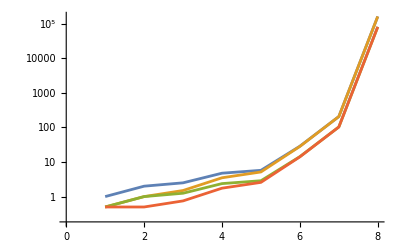

```mathematica
ListLogPlot[TestSemLatAsymp["orig"],Joined->True]
```

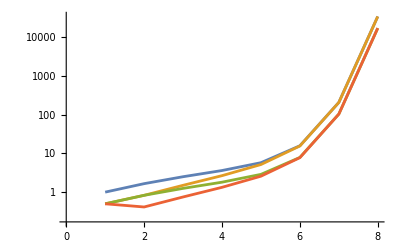

```mathematica
ListLogPlot[TestSemLatAsymp["smth"],Joined->True]
```

### Quasitrivial Semigroups

http://oeis.org/A292932 - Number of quasitrivial semigroups on an arbitrary n-element set. 
E.g.f.: 1/(x+3-2*exp(x)). -- exponential generating function
https://oeis.org/A292933 - E.g.f.: x/(x+3-2*exp(x)). -- with identity or with zero
https://oeis.org/A292934 - E.g.f.: x^2/(x+3-2*exp(x)).  -- with both identity and zero
Quasitrivial: a*b = one of a, b

N(“ident or zero”,n) = n*N(n-1)
N(“ident and zero”,n) = n*(n-1)*N(n-2)

https://arxiv.org/abs/1709.09162
Quasitrivial semigroups: characterizations and enumerations
Miguel Couceiro, Jimmy Devillet, Jean-Luc Marichal

Series base: 0

#### Data

```mathematica
NumData["smg qstv flip"] = {1,1,4,20,138,1182,12166,146050,2003882,30930734,530477310,10007736906,205965058162,4592120925862,110259944144486,2836517343551714,77836238876829882,2269379773783175454,70057736432648552782,2282895953541692345722};
```

```mathematica
NumData["smg qstv id flip"] = {0,1,2,12,80,690,7092,85162,1168400,18034938,309307340,5835250410,120092842872,2677545756106,64289692962068,1653899162167290,45384277496827424,1323216060906107994,40848835928097158172,1331096992220322502858};
```

```mathematica
NumData["smg qstv idzr flip"] = {0,0,2,6,48,400,4140,49644,681296,10515600,180349380,3402380740,70023004920,1561206957336,37485640585484,964345394431020,26462386594676640,771532717446066208,23817889096309943892,776127882633846005268};
```

#### Formulas

```mathematica
NumListVal["smg qstv flip",nmax_?IsNonNegInt] := Module[{a},
a[0] = 1;
Do[a[n] = n*a[n-1] + 2*Sum[Binomial[n,k]*a[k],{k,0,n-2}],{n,nmax}];
Array[a,nmax+1,0]
]
```

```mathematica
NumVal["smg qstv flip",n_?IsNonNegInt] := Sum[2^i*(-1)^k*Binomial[n,k]*StirlingS2[n-k,i]*(i+k)!,{i,0,n},{k,0,n-i}]
```

```mathematica
NumListVal["smg qstv flip gnf",nmax_?IsNonNegInt] := Block[{x},CoefficientList[Series[1/(3+x-2*Exp[x]),{x,0,nmax}],x]*Range[0,nmax]!]
```

```mathematica
(* Asymptotic formula *)
```

```mathematica
(* LambertW[-1,z] = ProductLog[z], solution for w in z = w*Exp[w] *)
```

```mathematica
NumQsTrAsyConst = - LambertW[-1,-2Exp[-3.]]
```

3.58307

```mathematica
NumAsymp["smg qstv flip",n_] := (c |-> n!/((c-1)(c-3)^(n+1))) @ NumQsTrAsyConst
```

#### Tests

```mathematica
(d |-> d - NumListVal["smg qstv flip",Length[d]-1]) @ NumData["smg qstv flip"] // Tally
```

{{0,20}}

```mathematica
ShiftMult[shf_,data_] := Join[ConstantArray[0,shf],Table[Product[n+k,{k,0,shf-1}],{n,Length[data]}]*data]
```

```mathematica
(d |-> d  - Take[ShiftMult[1,NumData["smg qstv flip"]],Length[d]]) @ NumData["smg qstv id flip"] // Tally
```

{{0,20}}

```mathematica
(d |-> d- Take[ShiftMult[2,NumData["smg qstv flip"]],Length[d]]) @ NumData["smg qstv idzr flip"] // Tally
```

{{0,20}}

### Simple Semigroups

From
Enumerating 0-simple semigroups
https://research-repository.st-andrews.ac.uk/handle/10023/23558

0-simple: Rees matrix semigroup
H-triv: with trivial group
w 0: no zero, with zero added on

No known formulas.

Series base: 1

#### Data

```mathematica
NumData["smg smpl 0-smpl"] = {0,1,3,3,9,3,18,3,33,23,30,3,151,3,46,189,294,3,487,3,1397,664,90,3,5648,3841,118,1917,11716,3,45398,3,31996,4503,186,204185,285790,3,226,9706,1116191,3,3583160,3,399960,3881357,318,3,30271239,29610810,15214393,35305,1757051,3,222104344,55205944,922866288,61480,486,3,1762675631,3,550,13190856618,13718901762,625728729,10187010096,3,22657053,163155,176974898340,3,823881619734,3,766,5836761933,69496618,2146892812097,356407493734,3,19580066324253,20677459330076,930,3,26419833132046,46093054629,1018,552177,464292341808739,3,2094085011265979,260383999114719,514299114,789124,1206,315901054341,10256563628288892,3,2597046185315768,97100184784203210,103611007719055260,3,222670079940176,3,208703812193138857,24357579732335554,1518,3,4188448777559775907,3,19091741727581499836,2059390,4201290929266046145,3,4212693723851078,10412895280125,6565200607,167692379464165700555,1866,1814914300200409639,1700378443600053588142,1745061194503344181720,1990,3619077,13963742950,51505577788824,6275790700072159443717,3,1203342802955800797357,4708924};
```

```mathematica
NumData["smg smpl H-triv"] = {0,1,2,2,5,2,12,2,18,19,24,2,116,2,40,184,229,2,420,2,1338,658,84,2,5230,3837,112,1862,11618,2,44594,2,30710,4498,180,204180,282970,2,220,9700,1101448,2,3577908,2,399718,3879780,312,2,30156838,29610806,15069848,35300,1756696,2,222070638,55205938,922263078,61474,480,2,1757017984,2,544,13190836800,13715458490,625728724,10186888516,2,22656374,163150,176878810270,2,823708035742,2,760,5834602820,69495720,2146892812092,356407038668,2,19578467831806,20677459128734,924,2,26404057549872,46093054624,1012,552172,464291948898156,2,2094063283672984,260383999114714,514297640,789118,1200,315901054336,10255839996389954,2,2595854189959052,97100184782573478,103610729300331610,2,222670075515736,2,208703805552811252,24357568048361550,1512,2,4188419057295337524,2,19091738417871913466,2059384,4200967305301010852,2,4212693711897014,10412895280120,6565197868,167692379464154875548,1860,1814914300200409634,1700377301105413386160,1745061194503344181716,1984,3619072,13963739668,51505321476420,6275751281470592125364,2,1203277350014102636584,4708918};
```

```mathematica
NumData["smg smpl w 0"] = {0,1,3,3,7,3,10,3,17,7,10,3,29,3,10,9,46,3,32,3,31,10,10,3,102,7,10,22,32,3,56,3,166,9,10,9,178,3,10,10,153,3,78,3,36,83,10,3,661,7,80,9,39,3,305,10,260,10,10,3,1431,3,10,243,1543,9,122,3,43,9,552,3,5763,3,10,2889,44,9,162,3,14566,736,10,3,14646,9,10,9,923,3,67314,9,48,10,10,9,185084,3,8219,1817,278968,3,248,3,1765,654268,10,3,1177657,3,11944,10,1202115,3,312,9,55,4507,10,9,28032758,7,10,9,56,2759049,65212924,3,10195549,10};
```

```mathematica
NumData["smg smpl grp w 0"] = {0,1,1,1,2,1,2,1,5,2,2,1,5,1,2,1,14,1,5,1,5,2,2,1,15,2,2,5,4,1,4,1,51,1,2,1,14,1,2,2,14,1,6,1,4,2,2,1,52,2,5,1,5,1,15,2,13,2,2,1,13,1,2,4,267,1,4,1,5,1,4,1,50,1,2,3,4,1,6,1,52,15,2,1,15,1,2,1,12,1,10,1,4,2,2,1,231,1,5,2,16,1,4,1,14,2,2,1,45,1,6,2,43,1,6,1,5,4,2,1,47,2,2,1,4,5,16,1,2328,2};
```

#### Tests

```mathematica
(d |-> d - FiniteGroupCount[Range[Length[d]]]) @ Rest[NumData["smg smpl grp w 0"]] // Tally
```

{{0,129}}

### Monoids

Has associativity, an identity.

Only a little bit of a known formula.

A monoid has a group part G and a semigroup part S. G acts on S, making permutations of the elements of S, though that may be different for G.S and S.G. If G has a trivial action, G.s = s.G = s for all s in A, then G’s action on S does not constrain S’s structure, and one can use counts of groups and semigroups to count such monoids.

https://oeis.org/A058129 - Number of monoids (semigroups with identity) of order n.
https://oeis.org/A058133 - Number of monoids (semigroups with identity) of order n, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator). 
https://oeis.org/A058131 - Number of commutative monoids (commutative semigroups with identity) of order n. 
https://oeis.org/A058132 - Number of self-converse monoids (semigroups with identity) of order n.
http://oeis.org/A058154 - Number of labeled monoids of order n with a fixed identity. 
http://oeis.org/A058153 - Number of labeled monoids of order n. 
http://oeis.org/A058156 - Number of labeled commutative monoids of order n with a fixed identity.
http://oeis.org/A058155 - Number of labeled commutative monoids of order n. 

https://oeis.org/A234844 - Number of inverse monoids of order n. 
https://oeis.org/A234845 - Number of commutative inverse monoids of order n.
http://oeis.org/A151823 - Number of nonequivalent monoids of order n with more than one invertible element 
(group part is nontrivial)
http://oeis.org/A176142 - Number of nonequivalent monoids of order n in which the action of the unit group on the maximal ideal is nontrivial.

Series base: 1

#### Data

```mathematica
NumData["mnd"] = {1,2,7,35,228,2237,31559,1668997};
```

```mathematica
NumData["mnd flip"] = {1,2,6,27,156,1373,17730,858977,1844075697,52991253973742};
```

```mathematica
NumData["mnd cmt"] = {1,2,5,19,78,421,2637};
```

```mathematica
NumData["mnd scnv"] = {1,2,5,19,84,509,3901,48957};
```

```mathematica
NumData["mnd lbl ifx"] = {1,2,11,156,4122,208672,18507440,7892741602};
```

```mathematica
NumData["mnd lbl"] = {1,4,33,624,20610,1252032,129552080,63141932606};
```

```mathematica
NumData["mnd cmt lbl ifx"] = {1,2,9,94,1486,38890,1430442};
```

```mathematica
NumData["mnd cmt lbl"] = {1,4,27,376,7430,233340,10013094};
```

```mathematica
NumData["mnd inv flip"] = {1,2,4,11,27,89,310,1311,6253,34325,212247,1466180,11167987,92889294,836021796};
```

```mathematica
NumData["mnd inv cmt"] = {1,2,4,11,27,87,300,1259,5988,32812,202784,1400541,10669344,88761928,799112310};
```

```mathematica
NumData["mnd ntvgrp flip"] = {0,1,2,9,30,213,1757,22956,955569,1853259264};
```

```mathematica
NumData["mnd ntvact flip"] = {0,0,0,2,5,58,428,5539,101082,9269715};
```

#### Tests

```mathematica
(* Test formula for nontrivial group part *)
```

```mathematica
NumData["mnd flip"] - (Take[NumData["smg flip"],Length[NumData["mnd flip"]]]+ NumData["mnd ntvgrp flip"]) // Tally
```

{{0,10}}

```mathematica
(* Test formula for nontrivial group action on the semigroup part *)
```

```mathematica
NumVal["mnd tvlact flip",n_] := Sum[FiniteGroupCount[k]*NumData["smg flip"][[n-k+1]],{k,1,n}]
```

```mathematica
NumData["mnd flip"] - (NumVal["mnd tvlact flip",Range[Length[NumData["mnd flip"]]]] + NumData["mnd ntvact flip"]) // Tally
```

{{0,10}}

### Idempotent Monoids

With idempotents.

No known formula.

https://oeis.org/A058137 - Triangle read by rows: monoids of order n with k idempotents.
https://oeis.org/A058147 - Triangle read by rows: number of monoids of order n with k idempotents, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator).
https://oeis.org/A058142 - Triangle read by rows: number of commutative monoids of order n with k idempotents.
https://oeis.org/A058144 - Triangle: Self-converse monoids of order n with k idempotents.
http://oeis.org/A058158 - Triangle: Labeled monoids of order n with k idempotents with a fixed identity.
http://oeis.org/A058157 - Triangle: Labeled monoids of order n with k idempotents.
http://oeis.org/A058160 - Triangle: Labeled commutative monoids of order n with k idempotents with a fixed identity. 
http://oeis.org/A058159 - Triangle: Labeled commutative monoids of order n with k idempotents. 

For idempotent monoids, uses idempotent semigroups with sequence locations bumped up. This is because the monoids are (identity) + (idempotent semigroup)

http://oeis.org/A058164 - Number of labeled lattices with a fixed bottom.
http://oeis.org/A055512 - Lattices with n labeled elements.

Kleitman, D. J., & Winston, K. J. (1980). The Asymptotic Number of Lattices. Annals of Discrete Mathematics, 243–249. doi:10.1016/s0167-5060(08)70708-8

#### Data

```mathematica
NumTriData["mnd idmp"] = MakeTriData[{1,1,1,1,3,3,2,9,14,10,1,32,63,86,46,2,219,406,694,665,251,1,5585,3331,6343,8582,6035,1682}];
```

```mathematica
NumTriData["mnd idmp flip"] = MakeTriData[{1,1,1,1,3,2,2,9,10,6,1,30,47,52,26,2,175,283,413,365,135,1,3333,2139,3630,4597,3155,875}];
```

```mathematica
NumTriData["mnd idmp cmt"] = MakeTriData[{1,1,1,1,3,1,2,9,6,2,1,26,30,16,5,1,98,142,111,54,15,1,455,718,713,482,215,53}];
```

```mathematica
NumTriData["mnd idmp scnv"] = MakeTriData[{1,1,1,1,3,1,2,9,6,2,1,28,31,18,6,2,131,160,132,65,19,1,1081,947,917,612,275,68}];
```

```mathematica
NumTriData["mnd idmp lbl ifx"] = MakeTriData[{1, 1, 1, 1, 6, 4, 4, 45, 72, 35, 6, 528, 1308, 1676, 604, 80, 19935, 39700, 70170, 62060, 16727, 120, 3599436, 1969470, 3829000, 5167800, 3260382, 681232}];
```

```mathematica
NumTriData["mnd idmp lbl"] = MakeTriData[{1,2,2,3,18,12,16,180,288,140,30,2640,6540,8380,3020,480,119610,238200,421020,372360,100362,840,25196052,13786290,26803000,36174600,22822674,4768624}];
```

```mathematica
NumTriData["mnd idmp cmt lbl ifx"] = MakeTriData[{1,1,1,1,6,2,4,45,36,9,6,408,648,348,76,60,7195,13500,11790,5280,1065,120,200016,369930,425280,293640,118890,22566}];
```

```mathematica
NumTriData["mnd idmp cmt lbl"] = MakeTriData[{1,2,2,3,18,6,16,180,144,36,30,2040,3240,1740,380,360,43170,81000,70740,31680,6390,840,1400112,2589510,2976960,2055480,832230,157962}];
```

```mathematica
NumData["mnd idmp"] = Prepend[NumData["smg idmp"],1];
```

```mathematica
NumData["mnd idmp flip"] = Prepend[NumData["smg idmp flip"] ,1];
```

```mathematica
NumData["mnd idmp cmt"] = Prepend[NumData["smg idmp cmt"] ,1];
```

```mathematica
NumData["mnd idmp scnv"] = Prepend[NumData["smg idmp scnv"] ,1];
```

```mathematica
NumData["mnd idmp lbl ifx"] = Prepend[NumData["smg idmp lbl"] ,1];
```

```mathematica
NumData["mnd idmp lbl"] = MultByIndex[NumData["mnd idmp lbl ifx"] ];
```

```mathematica
NumData["mnd idmp cmt lbl ifx"] = Prepend[NumData["smg idmp cmt lbl"] ,1];
```

```mathematica
NumData["mnd idmp cmt lbl"] = MultByIndex[NumData["mnd idmp cmt lbl ifx"] ];
```

#### Tests

```mathematica
NumTriData["mnd idmp lbl"] - MultByIndex[NumTriData["mnd idmp lbl ifx"]] // Flatten // Tally
```

{{0,28}}

```mathematica
NumTriData["mnd idmp cmt lbl"] - MultByIndex[ NumTriData["mnd idmp cmt lbl ifx"]] // Flatten // Tally
```

{{0,28}}

### Groups

Has  associativity, an identity, and division (inverses).

No known formula in general, formulas for 

https://oeis.org/A000001 - Number of groups of order n. 
https://oeis.org/A000688 - Number of Abelian groups of order n; number of factorizations of n into prime powers.
https://oeis.org/A058163 - Number of labeled groups with a fixed identity.
https://oeis.org/A034383 - Number of labeled groups. 
https://oeis.org/A058162 - Number of labeled Abelian groups with a fixed identity.
https://oeis.org/A034382 - Number of labeled Abelian groups of order n.
https://oeis.org/A058161 - Number of labeled cyclic groups with a fixed identity.
https://oeis.org/A034381 - Number of labeled cyclic groups. 
https://oeis.org/A066060 - Number of nilpotent groups of order n. 

[math/0605185] Automorphisms of finite Abelian groups
Christopher J. Hillar, Darren Rhea
https://arxiv.org/abs/math/0605185

https://oeis.org/A021002 - Decimal expansion of zeta(2)*zeta(3)*zeta(4)*... 
Asymptotic value of the mean number of abelian groups below some order

Series base: 1

#### Data

```mathematica
NumData["grp"] = {1,1,1,2,1,2,1,5,2,2,1,5,1,2,1,14,1,5,1,5,2,2,1,15,2,2,5,4,1,4,1,51,1,2,1,14,1,2,2,14,1,6,1,4,2,2,1,52,2,5,1,5,1,15,2,13,2,2,1,13,1,2,4,267,1,4,1,5,1,4,1,50,1,2,3,4,1,6,1,52,15,2,1,15,1,2,1,12,1,10,1,4,2};
```

```mathematica
NumData["grp cmt"] = {1,1,1,2,1,1,1,3,2,1,1,2,1,1,1,5,1,2,1,2,1,1,1,3,2,1,3,2,1,1,1,7,1,1,1,4,1,1,1,3,1,1,1,2,2,1,1,5,2,2,1,2,1,3,1,3,1,1,1,2,1,1,2,11,1,1,1,2,1,1,1,6,1,1,2,2,1,1,1,5,5,1,1,2,1,1,1,3,1,2,1,2,1,1,1,7,1,2,2,4,1,1,1,3,1,1,1};
```

```mathematica
NumData["grp lbl ifx"] = {1,1,1,4,6,80,120,2760,7560,108864,362880,21621600,39916800,1186099200,10897286400,647091244800,1307674368000,103742166528000,355687428096000,32438693442355200,260668072304640000,5573557327822848000,51090942171709440000};
```

```mathematica
NumData["grp lbl"] = {1,2,3,16,30,480,840,22080,68040,1088640,3991680,259459200,518918400,16605388800,163459296000,10353459916800,22230464256000,1867358997504000,6758061133824000,648773868847104000,5474029518397440000,122618261212102656000};
```

```mathematica
NumData["grp cmt lbl ifx"] = {1,1,1,4,6,60,120,1920,7560,90720,362880,13305600,39916800,1037836800,10897286400,265686220800,1307674368000,66691392768000,355687428096000,20274183401472000,202741834014720000};
```

```mathematica
NumData["grp cmt lbl"] = {1,2,3,16,30,360,840,15360,68040,907200,3991680,159667200,518918400,14529715200,163459296000,4250979532800,22230464256000,1200445069824000,6758061133824000,405483668029440000};
```

```mathematica
NumData["grp cyc lbl ifx"] = {1,1,1,3,6,60,120,1260,6720,90720,362880,9979200,39916800,1037836800,10897286400,163459296000,1307674368000,59281238016000,355687428096000,15205637551104000,202741834014720000,5109094217170944000,51090942171709440000};
```

```mathematica
NumData["grp cyc lbl"] = {1,2,3,12,30,360,840,10080,60480,907200,3991680,119750400,518918400,14529715200,163459296000,2615348736000,22230464256000,1067062284288000,6758061133824000,304112751022080000};
```

```mathematica
NumData["grp nil"] = {1,1,1,2,1,1,1,5,2,1,1,2,1,1,1,14,1,2,1,2,1,1,1,5,2,1,5,2,1,1,1,51,1,1,1,4,1,1,1,5,1,1,1,2,2,1,1,14,2,2,1,2,1,5,1,5,1,1,1,2,1,1,2,267,1,1,1,2,1,1,1,10,1,1,2,2,1,1,1,14,15,1,1,2,1,1,1,5,1,2,1,2,1,1,1,51,1,2,2,4,1};
```

#### Built-In, Abelian (Commutative), and Nilpotent Formulas

```mathematica
(* Check against built-in *)
```

```mathematica
NumVal["grp",n_?IsPosInt] := FiniteGroupCount[n]
```

```mathematica
NumVal["grp cmt",n_?IsPosInt] := FiniteAbelianGroupCount[n]
```

```mathematica
(* One cyclic group per order *)
```

```mathematica
NumVal["grp cyc",n___] := 1
```

```mathematica
(* Check abelian-group formulas *)
```

```mathematica
(* From OEIS: Times @@ PartitionsP /@ Last /@ FactorInteger @ n *)
```

```mathematica
NumVal["grp cmt x",n_?IsPosInt] := PrimePowerFunc[n,PartitionsP[#2]&]
```

```mathematica
NumVal["grp ppcyc",n_?IsPosInt] := If[n>1,Boole[PrimePowerQ[n]],1]
```

```mathematica
NumVal["grp ppcyc x",n_?IsPosInt] := If[Length[FactorInteger[n]]==1,1,0]
```

```mathematica
(* Check nilpotent-group formula - is every nilpotent group the product of distinct-prime p-groups? *)
```

```mathematica
NumVal["grp nil",n_?IsPosInt] := PrimePowerFunc[n,FiniteGroupCount[#1^#2]&]
```

```mathematica
(* Number of automorphisms of abelian groups with some set of prime powers *)
```

```mathematica
NumAutoMorphPrmPwrs[p_,pwrs_List] := Module[{psrt,n,ixtab,ixmin,ixmax},
psrt = Sort[pwrs];
n = Length[pwrs];
ixtab = Table[Select[Range[n],psrt[[#]]==psrt[[k]]&],{k,n}];
ixmin = Min /@ ixtab; ixmax = Max /@ ixtab;
Product[(p^ixmax[[k]]-p^(k-1))*p^(psrt[[k]]*(n-ixmax[[k]]) + (psrt[[k]]-1)*(n-ixmin[[k]]+1)),{k,n}]
]
```

```mathematica
NumVal["grp cmt lbl ifx",n_?IsPosInt] := (n-1)!*PrimePowerFunc[n,Sum[1/NumAutoMorphPrmPwrs[#1,pt],{pt,IntegerPartitions[#2]}]&]
```

```mathematica
NumVal["grp cmt lbl",n_?IsPosInt] := n*NumVal["grp cmt lbl ifx",n]
```

```mathematica
NumVal["grp cyc lbl ifx",n_?IsPosInt] := (n-1)!/EulerPhi[n]
```

```mathematica
NumVal["grp cyc lbl",n_?IsPosInt] := n*NumVal["grp cyc lbl ifx",n]
```

```mathematica
(* Asymptotic value of the average number of abelian groups per order *)
```

```mathematica
NumCmtGrpAsymp = Product[Zeta[N[n]],{n,2,100}]
```

2.29486

```mathematica
NumAsymp["grp cmt",n___] := NumCmtGrpAsymp
```

#### Prime Powers (p-groups)

```mathematica
(* Mathematica has powers of 2 up to 10, all other prime powers up to 7 *)
```

```mathematica
(* Prime-power order *)
```

```mathematica
NumVal["grp prmpwr",p_?PrimeQ,0] := 1
```

```mathematica
NumVal["grp prmpwr",p_?PrimeQ,1] := 1
```

```mathematica
NumVal["grp prmpwr",p_?PrimeQ,2] :=2
```

```mathematica
NumVal["grp prmpwr",p_?PrimeQ,3] :=5
```

```mathematica
NumVal["grp prmpwr",p_?PrimeQ,4] :=Which[p==2,14,True,15]
```

```mathematica
NumVal["grp prmpwr",p_?PrimeQ,5] :=Which[p==2,51,p==3,67,True,2p+61 + 2GCD[p-1,3] + GCD[p-1,4]]
```

```mathematica
NumVal["grp prmpwr",p_?PrimeQ,6] :=Which[p==2,267,p==3,504,True,3p^2+39*p+344 + 24GCD[p-1,3] + 11GCD[p-1,4] + 2GCD[p-1,5]]
```

```mathematica
NumVal["grp prmpwr",p_?PrimeQ,7] :=Which[p==2,2328,p==3,9310,p==5,34297,True,3p^5+12p^4+44p^3+170p^2+707p+2455 + (4p^2+44p+291)GCD[p-1,3] + (p^2+19p+135)GCD[p-1,4] + (3p+31)GCD[p-1,5]+ 4GCD[p-1,7]+5GCD[p-1,8]+GCD[p-1,9]]
```

```mathematica
(* Irreducible groups; those that are not direct powers of other groups *)
```

```mathematica
NumVal["grp ppird",p_?PrimeQ,0] :=1
```

```mathematica
NumVal["grp ppird",p_?PrimeQ,1] :=1
```

```mathematica
NumVal["grp ppird",p_?PrimeQ,2] :=1
```

```mathematica
NumVal["grp ppird",p_?PrimeQ,3] :=3
```

```mathematica
NumVal["grp ppird",p_?PrimeQ,4] :=Which[p==2,8,True,9]
```

```mathematica
NumVal["grp ppird",p_?PrimeQ,5] :=Which[p==2,34,p==3,49,True,2p +43 + 2GCD[p-1,3]+GCD[p-1,4]]
```

```mathematica
NumVal["grp ppird",p_?PrimeQ,6] :=Which[p==2,201,p==3,421,True,3p^2+37*p+267 + 22GCD[p-1,3] + 10GCD[p-1,4]+2GCD[p-1,5]]
```

```mathematica
NumVal["grp ppird",p_?PrimeQ,7] :=Which[p==2,2000,p==3,8727,p==5,33524,True,3p^5+12p^4+44p^3+167p^2+666p+2038 + (4p^2+44p+265)GCD[p-1,3] + (p^2+19p+123)GCD[p-1,4] + (3p+29)GCD[p-1,5]+ 4GCD[p-1,7]+5GCD[p-1,8]+GCD[p-1,9]]
```

```mathematica
TestPrmPwrGrp[n_Integer] := Table[Table[NumVal["grp prmpwr",p,m]-NumVal["grp",p^m],{m,7}],{p,Prime[Range[n]]}] // Tally
```

```mathematica
TestPrmPwrGrp[100]
```

{{{0,0,0,0,0,0,0},100}}

```mathematica
TestPrmPwrIrdGrp[n_Integer] := Table[NumVal["grp ppird",p,Range[7]] - PartIrredArray[NumVal["grp prmpwr",p,Range[7]]],{p,Prime[Range[n]]}] // Tally
```

```mathematica
TestPrmPwrIrdGrp[100]
```

{{{0,0,0,0,0,0,0},100}}

#### Multiple Primes in Group Order

```mathematica
areallprime[plst_] := And @@ (PrimeQ /@ plst)
```

Total f[p*q] = Irreducible f[p*q] + f[p]*f[q]

```mathematica
NumGrp["p11",prms_] := Module[{p,q},
If[!areallprime[prms],Return[]];
{p,q} = Sort[prms];
If[q == p,Return[NumVal["grp prmpwr",p,2]]];
If[Mod[q-1,p]==0,2,1]
]
```

```mathematica
NumGrp["p11 ird",prms_] := Module[{p,q},
If[!areallprime[prms],Return[]];
{p,q} = Sort[prms];
If[q == p,Return[NumVal["grp ppird",p,2]]];
If[Mod[q-1,p]==0,1,0]
]
```

```mathematica
TestNumGrp["p11",pnmax_] := Flatten[Table[NumGrp["p11",{p,q}] - {FiniteGroupCount[p*q],NumGrp["p11 ird",{p,q}]+1},{p,Prime[Range[pnmax]]},{q,Prime[Range[pnmax]]}],1] // Tally
```

Total f[p*q^2] = Irreducible f[p*q^2] + f[p]*f[q^2] + f[p*q]*f[q] + f[p]*f[q]^2 if q ≠ p, f[p^3] + f[p]*f[p^2] + f[p]^3 if q == p

```mathematica
NumGrp["p12",prms_] := Module[{p,q},
If[!areallprime[prms],Return[]];
{p,q} = prms;
If[q == p,Return[NumVal["grp prmpwr",p,3]]];
Which[p==2,5,p>2 && Mod[q-1,p]==0,(p+9)/2,p==3&&q==2,5,p>2 && q>2 && Mod[q+1,p]==0,3,p>3 && Mod[p-1,q]==0 && Mod[p-1,q^2]≠0,4,Mod[p-1,q^2]==0,5,Mod[q-1,p]≠0 && Mod[q+1,p]≠0 && Mod[p-1,q]≠0,2]
]
```

```mathematica
NumGrp["p12 ird",prms_] := Module[{p,q},
If[!areallprime[prms],Return[]];
{p,q} = prms;
If[q == p,Return[NumVal["grp ppird",p,3]]];
Which[p==2,2,p>2 && Mod[q-1,p]==0,(p+3)/2,p==3&&q==2,2,p>2 && q>2 && Mod[q+1,p]==0,1,p>3 && Mod[p-1,q]==0 && Mod[p-1,q^2]≠0,1,Mod[p-1,q^2]==0,2,Mod[q-1,p]≠0 && Mod[q+1,p]≠0 && Mod[p-1,q]≠0,0]
]
```

```mathematica
TestNumGrp["p12",pnmax_] := Flatten[Table[NumGrp["p12",{p,q}] - {FiniteGroupCount[p*q^2],NumGrp["p12 ird",{p,q}]+ If[q≠p,NumGrp["p11 ird",{p,q}],0] + NumVal["grp ppird",q,2] + 1},{p,Prime[Range[pnmax]]},{q,Prime[Range[pnmax]]}],1] // Tally
```

Total f[p*q*r] = Irreducible f[p*q*r] + f[p]*f[q*r] + f[q]*f[p*r] + f[r]*f[p*q] + f[p]*f[q]*f[r] if p,q,r all different, f[p*q^2] + f[p]*f[q^2] + f[q]*f[p*q] + f[p]*f[q]^2 if p ≠ q == r and likewise for appropriate permutations and f[p^3] + f[p]*f[p^2] + f[p]^3 for all equal

```mathematica
NumGrp["p111",prms_] := Module[{psrt,p,q,r,cqp,crp,crq},
If[!areallprime[prms],Return[]];
psrt = Sort[prms];
{p,q,r} = psrt;
If[q == p && r == p,Return[NumVal["grp prmpwr",p,3]]];
If[q == p,Return[NumGrp["p12",{r,p}]]];
If[r == p,Return[NumGrp["p12",{q,p}]]];
If[r == q,Return[NumGrp["p12",{p,q}]]];
cqp = Mod[q-1,p]==0; crp = Mod[r-1,p]==0; crq = Mod[r-1,q]==0;
If[cqp,If[crp,If[crq,p+4,p+2],If[crq,3,2]],If[crp,If[crq,4,2],If[crq,2,1]]]
]
```

```mathematica
NumGrp["p111 ird",prms_] := Module[{psrt,p,q,r,cqp,crp,crq},
If[!areallprime[prms],Return[]];
psrt = Sort[prms];
{p,q,r} = psrt;
If[q == p && r == p,Return[NumVal["grp ppird",p,3]]];
If[q == p,Return[NumGrp["p12 ird",{r,p}]]];
If[r == p,Return[NumGrp["p12 ird",{q,p}]]];
If[r == q,Return[NumGrp["p12 ird",{p,q}]]];
cqp = Mod[q-1,p]==0; crp = Mod[r-1,p]==0; crq = Mod[r-1,q]==0;
If[crp,If[cqp,p-1,0]+If[crq,1,0],0]
]
```

```mathematica
TestNumGrp["p111",pnmax_] := Flatten[Table[NumGrp["p111",{p,q,r}] - {FiniteGroupCount[p*q*r],NumGrp["p111 ird",{p,q,r}] + Which[p==q&&p==r,NumVal["grp ppird",p,2],q==r,NumVal["grp ppird",q,2] + NumGrp["p11 ird",{p,q}],p==r,NumVal["grp ppird",p,2] + NumGrp["p11 ird",{p,q}],p==q,NumVal["grp ppird",p,2] + NumGrp["p11 ird",{p,r}],True,NumGrp["p11 ird",{p,q}]+ NumGrp["p11 ird",{p,r}]+NumGrp["p11 ird",{q,r}]]+ 1},{p,Prime[Range[pnmax]]},{q,Prime[Range[pnmax]]},{r,Prime[Range[pnmax]]}],2] // Tally
```

#### Tests

```mathematica
(d |-> d - NumVal["grp",Range[Length[d]]]) @ NumData["grp"] // Tally
```

{{0,93}}

```mathematica
(d |->d - NumVal["grp cmt",Range[Length[d]]]) @ NumData["grp cmt"] // Tally
```

{{0,107}}

```mathematica
(* Test abelian-group formula *)
```

```mathematica
TestCmtGrp[n_?IsPosInt] := (nlst |-> NumVal["grp cmt x",nlst] - NumVal["grp cmt",nlst]) @ Range[n]
```

```mathematica
(* Test abelian-group prime-power formula *)
```

```mathematica
TestCmtGrpPrmPwr[n_?IsPosInt] := (nlst |-> NumVal["grp ppcyc x",nlst] -NumVal["grp ppcyc",nlst]) @ Range[n]
```

```mathematica
(* Test reduction of abelian prime-power groups *)
```

```mathematica
TestCmtGrpReduce[n_?IsPosInt] := (nlst |-> NumVal["grp ppcyc",nlst] - DivisorIrredArray[NumVal["grp cmt",nlst]]) @ Range[n]
```

```mathematica
TestCmtGrp[1000] // Tally
```

{{0,1000}}

```mathematica
TestCmtGrpPrmPwr[1000] // Tally
```

{{0,1000}}

```mathematica
TestCmtGrpReduce[100] // Tally
```

{{0,100}}

```mathematica
NumTest["grp nil",1] // Tally
```

{{0,101}}

```mathematica
NumTest["grp cmt lbl ifx",1] // Tally
```

{{0,21}}

```mathematica
NumTest["grp cmt lbl",1] // Tally
```

{{0,20}}

```mathematica
NumTest["grp cyc lbl ifx",1] // Tally
```

{{0,23}}

```mathematica
NumTest["grp cyc lbl",1] // Tally
```

{{0,20}}

## Graphs

```mathematica
MakePositive[xlst_] := (x |-> Max[x,1]) /@ xlst
```

```mathematica
ShowNums[lbls_] := ListLogPlot[MakePositive[NumData[#]]& /@ lbls,Joined->True,PlotRange->All,PlotLegends->lbls]
```

```mathematica
(* With the commutative subset *)
```

```mathematica
ShowNumCmt[lbl_] := ShowNums[{lbl,lbl<>" cmt"}]
```

```mathematica
(* With labeling and commutation *)
```

```mathematica
ShowNumCmtLbl[lbl_] := ShowNums[{lbl<>" lbl",lbl<>" cmt lbl",lbl,lbl<>" cmt"}]
```

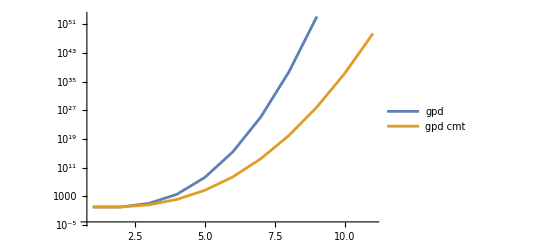
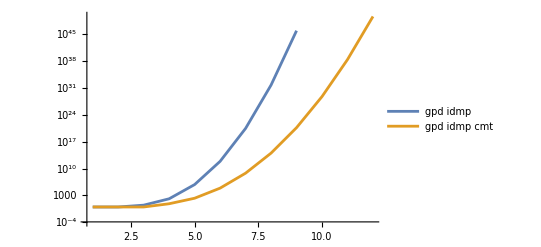
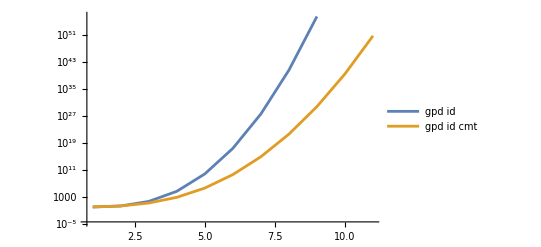
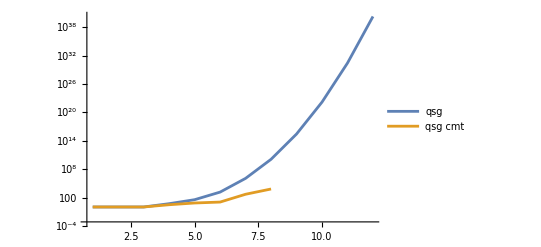
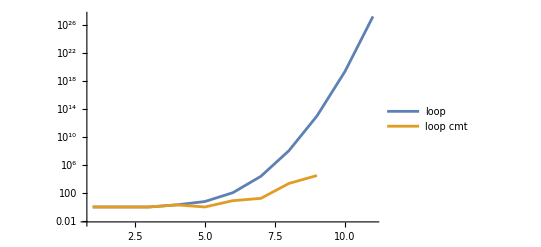
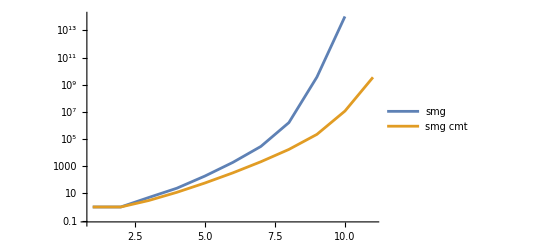
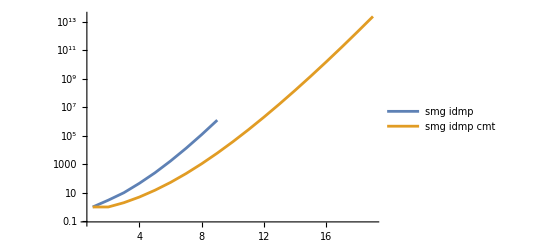
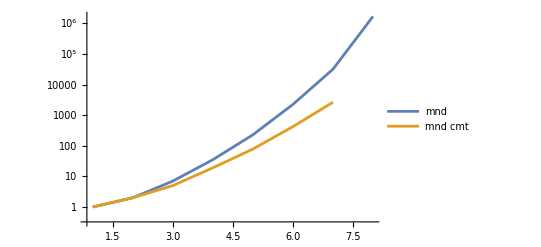

```mathematica
ShowNumCmt /@ {"gpd","gpd idmp","gpd id","qsg","loop","smg","smg idmp","mnd","mnd idmp"}
```

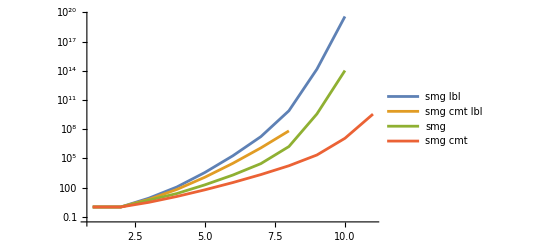
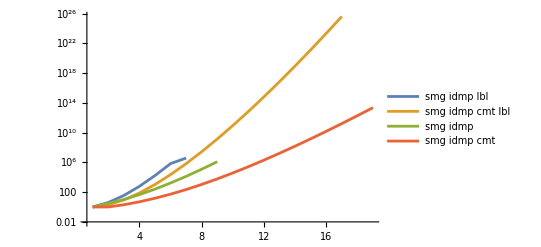
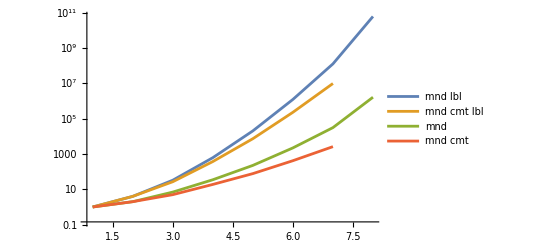
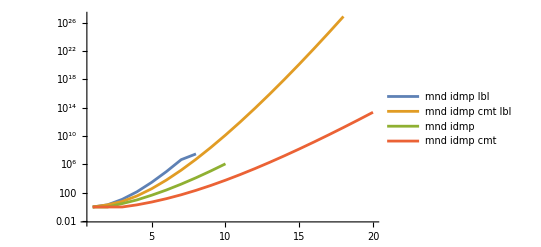

```mathematica
ShowNumCmtLbl /@ {"smg","smg idmp","mnd","mnd idmp"}
```

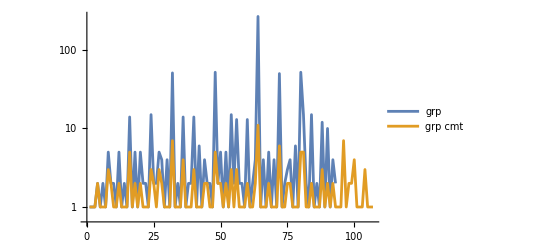

```mathematica
ShowNums[{"grp","grp cmt"}]
```

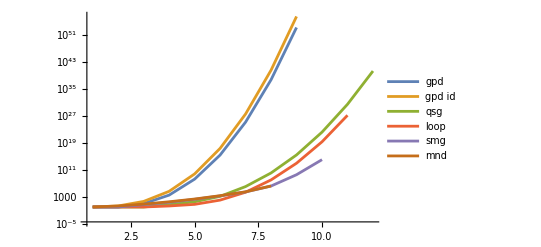

```mathematica
ShowNums[{"gpd","gpd id","qsg","loop","smg","mnd"}]
```

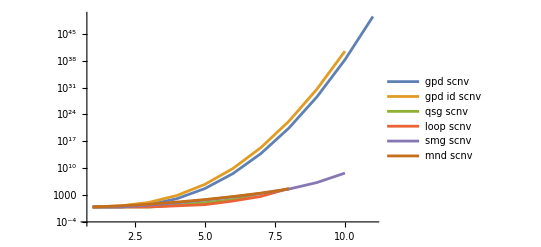

```mathematica
ShowNums[{"gpd scnv","gpd id scnv","qsg scnv","loop scnv","smg scnv","mnd scnv"}]
```

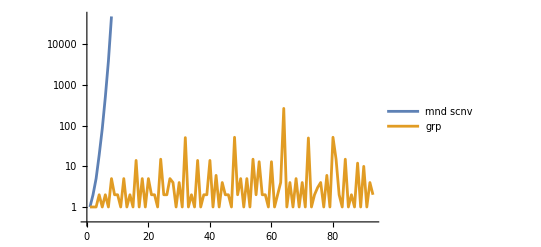

```mathematica
ShowNums[{"mnd scnv","grp"}]
```

## Estimated Asymptotic Behavior

### Factorial scaling between numbers for labeled and isomorphic algebras

```mathematica
(* Factorial scaling between labeled and isomorphic numbers? *)
```

```mathematica
FactorialSclData[lbl_,nbase_] := Module[{lbld,isom,mnlen},
lbld = NumData[lbl <> " lbl"];
isom = NumData[lbl];
mnlen = Min[Length[lbld],Length[isom]];
lbld = Take[lbld,mnlen];
isom = Take[isom,mnlen];
(isom*((Range[mnlen]-1+nbase)!) - lbld)/N[lbld]
]
```

```mathematica
FactorialSclVal[lbl_,nbase_,nmax_] := Table[(NumVal[lbl,n]*n! - #)/N[#]& @ NumVal[lbl<>" lbl",n],{n,nbase,nmax}]
```

```mathematica
FactorialSclVal["gpd",0,10]
```

{0.,0.,0.25,0.0150892,0.000139594,2.70363×10^-7,3.78021×10^-10,3.37165×10^-13,2.0235×10^-16,8.71652×10^-20,2.8247×10^-23}

```mathematica
FactorialSclVal["gpd cmt",0,10]
```

{0.,0.,0.,0.0617284,0.00634766,0.000459076,0.0000224226,8.20008×10^-7,2.38172×10^-8,5.71707×10^-10,1.16827×10^-11}

```mathematica
FactorialSclVal["gpd idmp",1,10]
```

{0.,0.5,0.135802,0.00234222,7.52231×10^-6,1.15678×10^-8,1.26941×10^-11,9.09549×10^-15,4.55614×10^-18,1.68365×10^-21}

```mathematica
FactorialSclVal["gpd idmp cmt",1,10]
```

{0.,0.,0.555556,0.125,0.0119782,0.000717069,0.0000311348,1.07133×10^-6,2.98843×10^-8,6.96342×10^-10}

```mathematica
FactorialSclVal["gpd id",1,10]
```

{0.,0.,0.111111,0.00634766,0.0000577987,1.57184×10^-7,2.43871×10^-10,2.2997×10^-13,1.44066×10^-16,6.42261×10^-20}

```mathematica
FactorialSclVal["gpd id cmt",1,10]
```

{0.,0.,0.111111,0.0546875,0.00663296,0.000465077,0.000022158,8.03294×10^-7,2.32431×10^-8,5.57074×10^-10}

```mathematica
FactorialSclData["qsg",0]
```

{0.,0.,0.,1.5,0.458333,0.0498512,0.00139155,0.0000129719,2.45852×10^-8,1.04653×10^-11,5.27961×10^-16,8.95735×10^-21}

```mathematica
FactorialSclData["loop",1]
```

{0.,0.,1.,2.,1.57143,0.390306,0.00915118,0.00020923,3.39818×10^-7,4.78143×10^-10}

```mathematica
FactorialSclData["smg",0]
```

{0.,0.,0.25,0.274336,0.292096,0.250735,0.20839,0.0594611,0.00232638,0.000259988}

```mathematica
FactorialSclData["smg cmt",0]
```

{0.,0.,0.,0.142857,0.221053,0.269118,0.301997,0.313177}

```mathematica
FactorialSclData["smg idmp",1]
```

{0.,0.5,0.714286,0.827815,0.800682,0.77772,16.4387}

```mathematica
FactorialSclData["smg idmp cmt",1]
```

{0.,0.,0.333333,0.578947,0.690141,0.69104,0.658556,0.608628,0.560476,0.520208,0.487597,0.461866,0.441649,0.425735,0.413146,0.403133,0.395134}

```mathematica
FactorialSclVal["smg nil3",3,10]
```

{0.,0.2,0.208191,0.0886526,0.0174736,0.0019296,0.000259009,0.0000384676}

```mathematica
FactorialSclVal["smg nil3 cmt",3,10]
```

{0.,0.428571,0.703704,0.661456,0.386499,0.167447,0.0678149,0.0261778}

```mathematica
FactorialSclData["slt",0]
```

{0.,0.,0.428571,0.868852,0.780645,0.270021,0.0263151,0.000355935}

```mathematica
FactorialSclData["slt noid",0]
```

{0.,0.,0.5,0.866667,0.743725,0.264904,0.026288,0.000355934}

```mathematica
FactorialSclData["slt nozr",0]
```

{0.,0.,0.428571,0.868852,0.780645,0.270021,0.0263151,0.000355935}

```mathematica
FactorialSclData["slt noidzr",0]
```

{0.,0.,0.5,0.866667,0.743725,0.264904,0.026288,0.000355934}

```mathematica
FactorialSclData["mnd",1]
```

{0.,0.,0.272727,0.346154,0.327511,0.286421,0.227748,0.065757}

```mathematica
FactorialSclData["mnd cmt",1]
```

{0.,0.,0.111111,0.212766,0.259758,0.299049,0.32731}

```mathematica
FactorialSclData["mnd idmp",1]
```

{0.,0.,0.5,0.714286,0.827815,0.800682,0.77772,16.4387}

```mathematica
FactorialSclData["mnd idmp cmt",1]
```

{0.,0.,0.,0.333333,0.578947,0.690141,0.69104,0.658556,0.608628,0.560476,0.520208,0.487597,0.461866,0.441649,0.425735,0.413146,0.403133,0.395134}

### Scaling of Latin squares, quasigroups, and loops

```mathematica
(* Number of Latin squares with size ≥ 1 *)
```

```mathematica
NumLatSqr = N[Rest[NumData["qsg lbl"]]];
```

```mathematica
(* Factorials of index values in this list*)
```

```mathematica
NumLSFctrl = N[Range[Length[NumLatSqr]]!];
```

```mathematica
(* isomorphism classes *)
```

```mathematica
Rest[NumData["qsg"]]/(NumLatSqr/NumLSFctrl)
```

{1.,1.,2.5,1.45833,1.04985,1.00139,1.00001,1.,1.,1.,1.}

```mathematica
(* isotopy classes -- separate row, column, symbol interchange *)
```

```mathematica
NumData["loop lbl rcspm"]/(NumLatSqr/NumLSFctrl^3)
```

{1.,4.,18.,48.,21.4286,10.102,1.17447,1.01012,1.00001,1.,1.}

```mathematica
(* isotopy with transpose *)
```

```mathematica
NumData["loop lbl rcstppm"]/(NumLatSqr/(2*NumLSFctrl^3))
```

{2.,8.,36.,96.,42.8571,15.6122,1.34939,1.01505,1.00003,1.,1.}

```mathematica
(* main classes -- interchange between rows, columns, symbols *)
```

```mathematica
NumData["loop lbl rcsallpm"]/(NumLatSqr/(6*NumLSFctrl^3))
```

{6.,24.,108.,288.,128.571,33.0612,1.83667,1.02559,1.00007,1.,1.}

### Labeled nilpotent degree-3 semigroups

```mathematica
(* For Latin squares, quasigroups, loops, semigroups, monoids, and groups in general, there is too little to go on *)
```

```mathematica
numval["smg nil3 lbl num",n_?ispzint] := If[n>0,Sum[Binomial[n,m]*m*Sum[(-1)^k*Binomial[m-1,k]*(m-k)^N[(n-m)^2],{k,0,m-1}],{m,2,Floor[n+1/2-Sqrt[n-3/4]]}],0]
```

```mathematica
numval["smg nil3 cmt lbl num",n_?ispzint] := If[n>0,Sum[Binomial[n,m]*m*Sum[(-1)^k*Binomial[m-1,k]*(m-k)^N[(n-m)*(n-m+1)/2],{k,0,m-1}],{m,2,Floor[n+3/2-Sqrt[2n+1/4]]}],0]
```

```mathematica
numval["smg nil3 lbl nmtest",n_?ispzint] := numval["smg nil3 lbl num",n]/(n^((1/2)n^2))
```

```mathematica
numval["smg nil3 cmt lbl nmtest",n_?ispzint] := numval["smg nil3 cmt lbl num",n]/(n^((1/4)n^2))
```

```mathematica
Log[numval["smg nil3 lbl num",Range[100]]]/Log[Range[100]]
```

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,1/Log[2]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[3]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[4]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[5]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[6]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[7]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[8]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[9]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[10]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[11]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[12]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[13]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[14]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[15]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[16]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[17]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[18]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[19]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[20]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[21]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[22]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[23]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[24]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[25]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[26]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[27]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[28]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[29]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[30]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[31]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[32]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[33]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[34]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[35]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[36]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[37]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[38]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[39]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[40]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[41]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[42]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[43]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[44]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[45]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[46]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[47]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[48]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[49]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[50]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[51]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[52]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[53]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[54]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[55]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[56]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[57]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[58]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[59]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[60]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[61]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[62]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[63]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[64]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[65]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[66]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[67]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[68]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[69]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[70]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[71]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[72]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[73]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[74]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[75]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[76]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[77]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[78]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[79]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[80]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[81]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[82]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[83]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[84]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[85]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[86]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[87]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[88]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[89]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[90]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[91]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[92]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[93]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[94]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[95]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[96]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[97]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[98]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[99]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[100]Log[numval[smg nil3 lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]]}

```mathematica
Differences[%]
```

```mathematica
Differences[%]
```

```mathematica
ListPlot[%]
```

-Graphics-

```mathematica
Log[numval["smg nil3 cmt lbl num",Range[100]]]/Log[Range[100]]
```

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,1/Log[2]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[3]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[4]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[5]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[6]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[7]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[8]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[9]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[10]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[11]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[12]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[13]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[14]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[15]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[16]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[17]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[18]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[19]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[20]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[21]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[22]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[23]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[24]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[25]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[26]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[27]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[28]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[29]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[30]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[31]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[32]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[33]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[34]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[35]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[36]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[37]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[38]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[39]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[40]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[41]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[42]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[43]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[44]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[45]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[46]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[47]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[48]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[49]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[50]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[51]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[52]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[53]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[54]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[55]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[56]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[57]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[58]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[59]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[60]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[61]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[62]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[63]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[64]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[65]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[66]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[67]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[68]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[69]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[70]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[71]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[72]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[73]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[74]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[75]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[76]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[77]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[78]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[79]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[80]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[81]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[82]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[83]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[84]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[85]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[86]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[87]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[88]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[89]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[90]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[91]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[92]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[93]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[94]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[95]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[96]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[97]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[98]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[99]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]],1/Log[100]Log[numval[smg nil3 cmt lbl num,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]]}

```mathematica
Differences[%]
```

```mathematica
Differences[%]
```

```mathematica
ListPlot[%]
```

-Graphics-

### Semigroups that are not nil-2 ones, nil-3 ones, or monoids

```mathematica
(* Remainder after nil-2 and nil-3 removed *)
```

```mathematica
NumSmgpRmdr[lbl_] := Module[{smg,nvals,diff},
smg = NumData["smg"<>lbl];
nvals = Range[Length[smg]]-1;
diff = smg - (1 + NumVal["smg nil3"<>lbl,nvals]);
{nvals,diff,diff/N[smg]}
]
```

```mathematica
(* Remainder after nil-2, nil-3, and monoids removed *)
```

```mathematica
NumSmgpMndRmdr[lbl_] := Module[{smg,mnd,lnmin,nvals,diff},
smg = NumData["smg"<>lbl];
mnd = Join[{0,0},Drop[NumData["mnd"<>lbl],1]];
lnmin = Min[Length[smg],Length[mnd]];
smg = Take[smg,lnmin];
mnd = Take[mnd,lnmin];
nvals = Range[lnmin]-1;
diff = smg - (1 + NumVal["smg nil3"<>lbl,nvals]+ mnd);
{nvals,diff,diff/N[smg]}
]
```

```mathematica
NumSmgpRmdr[""]
```

{{0,1,2,3,4,5,6,7,8,9},{0,0,4,22,178,1796,23962,427682,22507624,46305907836},{0.,0.,0.8,0.916667,0.946809,0.937859,0.836837,0.262757,0.00610951,0.000436938}}

```mathematica
NumSmgpMndRmdr[""]
```

{{0,1,2,3,4,5,6,7,8},{0,0,2,15,143,1568,21725,396123,20838627},{0.,0.,0.4,0.625,0.760638,0.818799,0.758713,0.243368,0.00565648}}

```mathematica
NumSmgpRmdr[" cmt"]
```

{{0,1,2,3,4,5,6,7,8,9,10},{0,0,2,10,52,301,1987,15184,141807,2195602,141655715},{0.,0.,0.666667,0.833333,0.896552,0.926154,0.927205,0.878145,0.639332,0.190164,0.0402553}}

```mathematica
NumSmgpMndRmdr[" cmt"]
```

{{0,1,2,3,4,5,6,7},{0,0,0,5,33,223,1566,12547},{0.,0.,0.,0.416667,0.568966,0.686154,0.730751,0.725638}}

```mathematica
NumSmgpRmdr[" scnv"]
```

{{0,1,2,3,4,5,6,7,8,9},{0,0,2,10,56,354,2662,24764,358586,17395172},{0.,0.,0.666667,0.833333,0.875,0.874074,0.803744,0.558125,0.162268,0.0278996}}

```mathematica
NumSmgpMndRmdr[" scnv"]
```

{{0,1,2,3,4,5,6,7,8},{0,0,0,5,37,270,2153,20863,309629},{0.,0.,0.,0.416667,0.578125,0.666667,0.65006,0.470205,0.140114}}

```mathematica
NumSmgpRmdr[" lbl"]
```

{{0,1,2,3,4,5,6,7,8,9},{0,0,7,106,3311,172011,13971867,1798975991,847072308385,16761524547060829},{0.,0.,0.875,0.938053,0.948167,0.936206,0.81893,0.232334,0.00571592,0.00043596}}

```mathematica
NumSmgpMndRmdr[" lbl"]
```

{{0,1,2,3,4,5,6,7,8},{0,0,3,73,2687,151401,12719835,1669423911,783930375779},{0.,0.,0.375,0.646018,0.769473,0.824032,0.745545,0.215603,0.00528984}}

```mathematica
NumSmgpRmdr[" cmt lbl"]
```

{{0,1,2,3,4,5,6,7},{0,0,5,56,1055,29109,1117901,58707781},{0.,0.,0.833333,0.888889,0.925439,0.94725,0.943319,0.884644}}

```mathematica
NumSmgpMndRmdr[" cmt lbl"]
```

{{0,1,2,3,4,5,6,7},{0,0,1,29,679,21679,884561,48694687},{0.,0.,0.166667,0.460317,0.595614,0.705467,0.74642,0.73376}}

### Monoids that are not trivial-action group-semigroup combinations

```mathematica
Range[Length[NumData["mnd flip"]]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
NumData["mnd flip"] - NumVal["mnd tvlact flip",%]
```

{0,0,0,2,5,58,428,5539,101082,9269715}

```mathematica
%/N[NumData["mnd flip"]]
```

{0.,0.,0.,0.0740741,0.0320513,0.0422433,0.0241399,0.00644837,0.0000548145,1.74929×10^-7}

### Average Number of Groups

```mathematica
(* Summation done recursively to avoid loss of significance *)
```

```mathematica
sumf[f_,n1_,n2_] := Which[n2>n1,Block[{nm1,nm2},nm1 = Floor[(n1+n2)/2];nm2 = nm1+1; sumf[f,n1,nm1] + sumf[f,nm2,n2]], n2==n1,f[n1],True,0]
```

```mathematica
(* For averaging group counts with weight 1/n and for skipping over missing values *)
```

```mathematica
abgavf[n_] := {1,FiniteAbelianGroupCount[n]}/N[n]
```

```mathematica
grpavf[n_] := Block[{ng},ng = FiniteGroupCount[n];
If[Head[ng] === Integer,{1,ng}/N[n],{0.,0.}]
]
```

```mathematica
avgsum[x_] := x[[2]]/x[[1]]
```

```mathematica
abgavg[nmax_] := avgsum[sumf[abgavf,1,nmax]]
```

```mathematica
grpavg[nmax_] := avgsum[sumf[grpavf,1,nmax]]
```

```mathematica
agagasymp[nmax_] := Block[{z,zprod = 1.},Do[z = Zeta[N[k]]; If[z ==1,Break[]]; zprod *=z,{k,2,nmax}];zprod]
```

```mathematica
agagasymp[1000]
```

2.29486

## Table Display

```mathematica
(* Label or array, how many *)
```

```mathematica
DisplayValues[x_,n_] := Switch[Head[x],String,Take[NumData[x],n],_,Array[x,n]]
```

```mathematica
DisplayValueList[xlst_,n_] := Table[DisplayValues[x,n],{x,xlst}]
```

```mathematica
DisplayTitledValueList[xlst_,n_,ninit_] := TableForm[Transpose[DisplayValueList[xlst,n]],TableHeadings->{Range[n]-1+ninit,xlst}]
```

```mathematica
DisplayTitledValueList[{"gpd lbl","gpd","gpd cmt lbl","gpd scnv","gpd cmt"},5,0]
```

| gpd lbl | gpd | gpd cmt lbl | gpd scnv | gpd cmt
0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1
2 | 16 | 10 | 8 | 4 | 4
3 | 19683 | 3330 | 729 | 138 | 129
4 | 4294967296 | 178981952 | 1048576 | 60160 | 43968

```mathematica
DisplayTitledValueList[{"gpd id lbl","gpd id","gpd id cmt lbl","gpd id scnv","gpd id cmt"},5,1]
```

| gpd id lbl | gpd id | gpd id cmt lbl | gpd id scnv | gpd id cmt
1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 2 | 4 | 2 | 2
3 | 243 | 45 | 81 | 15 | 15
4 | 1048576 | 43968 | 16384 | 944 | 720
5 | 762939453125 | 6358196250 | 48828125 | 725500 | 409600

```mathematica
DisplayTitledValueList[{"qsg lbl","qsg","qsg scnv","qsg cmt"},7,0]
```

| qsg lbl | qsg | qsg scnv | qsg cmt
0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1
3 | 12 | 5 | 3 | 3
4 | 576 | 35 | 13 | 7
5 | 161280 | 1411 | 81 | 11
6 | 812851200 | 1130531 | 3883 | 491

```mathematica
DisplayTitledValueList[{"loop lbl","loop","loop scnv","loop cmt"},7,1]
```

| loop lbl | loop | loop scnv | loop cmt
1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1
4 | 16 | 2 | 2 | 2
5 | 280 | 6 | 4 | 1
6 | 56448 | 109 | 35 | 8
7 | 118594560 | 23746 | 556 | 17

```mathematica
DisplayTitledValueList[{"loop lbl","loop lbl rcspm","loop lbl rcstppm","loop lbl rcsallpm"},7,1]
```

| loop lbl | loop lbl rcspm | loop lbl rcstppm | loop lbl rcsallpm
1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1
4 | 16 | 2 | 2 | 2
5 | 280 | 2 | 2 | 2
6 | 56448 | 22 | 17 | 12
7 | 118594560 | 564 | 324 | 147